# 3. Introduction to Linear Partial Differential Equations

In this chapter we will derive analytic solutions to some of the common linear partial differential equations (PDEs) of mathematical physics. We will first examine PDEs in one spatial dimension, focusing on the wave equation and the heat equation.We will then solve a PDE in more than one spatial dimension:  Laplace's equation. Finally, we will consider solutions of the wave and heat equations in more than one dimension.

For the simple cases discussed in this chapter, we will find that solutions can be obtained in terms of Fourier series, using the method of separation of variables.

## 3.1 Separation of Variables and Fourier Series Methods in Solutions of the Wave and Heat Equations

3.1.1 Derivation of the Wave Equation

## Introduction

The first partial differential equation that we will discuss is the wave equation in one dimension. This equation describes (among other things) the transverse vibrations of a string under tension, such as a guitar or violin string. In the next two sub-subsections we will derive the wave equation for a string,  from first principles.

## String Equilibrium

Consider a string, stretched tight in the x-direction between posts at x=0 and x=L. (See Fig. 3.1.) The tension in the string at point x is T(x).  Tension is a force, and so has units of newtons.  The tension T(x) at point x is defined as the force pulling on the piece of string to the left of point x  as it is acted on by  the string to the right of this point (see Fig. 3.1).  According to Newton's third law,  the force acting on the string to the right of point x  as it is pulled by the string on the left is -T(x): the forces of the two sections acting on one another are equal and opposite.  Furthermore, tension always acts in the direction along the string. We will define positive tension forces as those acting to the right- in the positive x-direction.

Fig. 3.1 Equilibrium of a string.

The string in Fig. 3.1 is in equilibrium. In equilibrium, in the absence of gravity or other such external forces, the tension in the string is uniform, and the string is perfectly straight. This can be understood from the following argument. Consider an element of the string with mass ⅆm and length ⅆx , running from x to x+ⅆx . If the string is straight, but the tension in the string is a function of position, then the tension pulling the element to the right is T(x+ⅆx) and that pulling the element to the left is -T(x) (see Fig. 3.2). However, in equilibrium, the total force on ⅆm must vanish, so T(x+ⅆx)-T(x)=0, and therefore T must be independent of position in equilibrium. Also, since we have achieved force balance with a straight string, we have shown that a straight string is in equilibrium.

Fig. 3.2 Forces acting on a mass element in equilibrium.

However, if an extra force ⅆF, such as gravity,  acts on the element ⅆm in the x direction then T is not constant in equilibrium. Equilibrium force balance then yields  T(x+ⅆx)+ⅆF-T(x)=0. Taylor expansion of this expression implies

ⅆT/ⅆx=-ⅆF/ⅆx.

For instance, if gravity points in the -x direction, then ⅆF=-ⅆm g. Equation (3.1.1) then implies that ⅆT/ⅆx=ρ g, where

ρ(x)=ⅆm/ⅆx

is the mass per unit length.  In this example the tension increases with increasing x, because more of the string weight must be supported by the remaining string as one moves up the string against gravity,  in the +x direction.

Since all forces have been assumed to act along the x-direction, the string remains straight. However, if time-independent forces, such as a force of gravity in the y direction, act transverse to the string it will no longer remain straight in equilibrium, but will sag under the action of the transverse force. (This can be observed "experimentally" in spring-mass simulations of an elastic string, in Sec. 9.10.)  In what follows, we neglect the effect of such forces on the equilibrium of the string, and assume that the equilibrium is a straight horizontal string along the x -axis, following the equation y=0. We will examine the effect of a gravitational force in the y-direction in Sec. 3.1.2.

## String Dynamics: The Wave Equation

Now let us consider a string that has been perturbed away from equilibrium by a small transverse displacement in the y -direction. The shape of the string is now a curve that changes with time, given by the function y(x,t). (See Fig. 3.3.)  Our job is to obtain an equation of motion for y(x,t).  To simplify this task, we will assume that the perturbed string is nearly straight: |∂y/∂x|<<1 .

Fig. 3.3 Forces acting on a mass element in motion (displacement greatly exaggerated for ease of viewing).

The equation of motion for y(x,t) can be found by applying Newton's second law to the motion of an element ⅆm of the string, located between x and x+ⅆx . The total force ⅆ F_y  in the y-direction on this element is determined by the y-component of the tension T_y(x,t) acting on each end of the string (assuming that no forces other than tension act in the y-direction):

ⅆ F_y=T_y(x+ⅆx,t)-T_y(x,t)=ⅆx ∂/(∂x)T_y(x,t).

By Newton's second law, this force determines the acceleration of the mass element in the y-direction:

ⅆm ∂^2/(∂t^2)y(x,t)=ⅆ F_y =ⅆx∂/(∂x)T_y(x,t).

Because tension forces act along the direction of the string, the y-component of the tension is related to the displacement of the string from equilibrium. According to Fig. 3.3,  T_y(x,t)=T(x,t) sinθ, where T(x,t) is the magnitude of the tension in the string at position x and time t, and θ is the angle of the element ⅆm with respect to the horizontal. However, since the displacement from equilibrium is assumed small, θ must also be small, and therefore sinθ≈θ, which implies that

T_y(x,t)≈T(x,t) θ .

Furthermore, according to Fig. 3.3,  θ is related to the displacement of the string through tanθ = ∂y/∂x . For small angles tanθ≈θ, so this implies θ≈ ∂y/∂x. Combining this result with Eq. (3.1.5), we obtain T_y(x,t)≈T(x,t) ∂y/∂x . However, as we are interested only in small-amplitude transverse displacements of the string, we can replace T(x,t) by the equilibrium tension T(x). Therefore, we obtain

T_y(x,t)≈T(x) ∂y/∂x.

Applying this result to Eq. (3.1.4),  dividing by ⅆm,  and using Eq. (3.1.2) yields

∂^2/(∂t^2)y(x,t)=1/(ρ(x))∂/(∂x)(T(x) ∂/(∂x)y(x,t)).

Equation (3.1.7) is the wave equation for a string with equilibrium tension T(x) and mass per unit length ρ(x). This equation describes the evolution of small transverse displacements y(x,t) away from equilibrium. The equation is a linear partial differential equation in the unknown function y(x,t), and is second order in time and second order in space. Since the equation is second-order in space, two boundary conditions are required: the ends of the string are fixed by the posts at each end so y=0 at x=0 and at x=L.

Since the wave equation is second-order in time, two initial conditions are also  needed. The position and transverse velocity of each element of the string must be specified initially in order to determine its subsequent motion. In other words, we require knowledge of y(x,t=0) and ∂/(∂t)y(x,t=0) for all x in the range 0<x<L. Thus, the solution of the wave equation is specified by boundary conditions

y(0,t)=y(L,t)=0

and by initial conditions

y(x,0)=y_o(x),
(∂y)/(∂t)(x,0)=v_o(x),

for some initial transverse displacement y_o(x) and initial transverse velocity v_o(x).

The wave equation can be simplified in the case that the string tension is uniform [T(x) = T] and the mass density is also uniform [ρ(x) = ρ]. Then Eq. (3.1.7) becomes

∂^2/(∂t^2)y(x,t)=c^2 ∂^2/(∂x^2)y(x,t).

The constant c is

c=√(T/ρ),

and has units of a velocity. In fact we will see that this quantity is the speed at which transverse disturbances propagate along the string.

The magnitude of c depends on the mass density and thickness of the string as well as the tension to which is it subjected .  For instance,  the high E string on a steel string guitar is typically made of steel with a mass density ℳ of roughly ℳ=7.5 g/cm^3. The radius of this string is r=0.15 mm, giving a mass per unit length of

ρ = π r^2 ℳ=0.0053 g/cm=5.3×10^-4 kg/m.

According to Eq. (3.1.11), a tension of T= 500 N yields a speed of c=970 m/s.

Although we have derived the wave equation for transverse waves on a string, the same PDE also applies to many other types of wave disturbances traveling in one spatial dimension. For example, the equation applies to the small-amplitude waves on the surface of shallow water (neglecting surface tension), with y(x,t) now the height of the water surface [see Exercise (4) at the end of this section]. The equation also applies to pressure waves propagating through a medium such as air, with y(x,t) now the pressure or density in the medium.   The equation applies to propagation of electromagnetic waves such as visible light or radio waves, with y(x,t) now identified with the electric or magnetic field in the wave. The wave equation itself is the same in each case, even though the physical processes for each type of wave are very different.  Of course, in each instance, the speed of propagation c differs. Obviously, for sound waves c is the speed of sound, but for light waves c is the speed of light.

3.1.2 Solution of the Wave Equation Using Separation of Variables

## Solution of the Wave Equation for a Uniform String and Fixed Ends

#### Separation of Variables for a Uniform String

We will now solve the wave equation for a uniform string, Eq. (3.1.10), with boundary conditions that the ends are fixed:  y=0 at x=0 and x=L, and initial conditions given by Eq.  (3.1.9).  To solve this problem, we will apply the method of separation of variables. In this method, we look for a solution to the PDE of the form

y(x,t)=f(t)ψ(x),

where f(t) and ψ(x) are some functions that need to be determined in order to satisfy the PDE and match the boundary and initial conditions. In fact, we will find that there are many possible solutions of this form, each of which satisfy the PDE and the boundary conditions.  We will create a superposition of these solutions in order to match the initial conditions.

If we substitute  Eq. (3.1.13) into the wave equation, Eq. (3.1.10), and then divide by f(t) ψ(x), we obtain

1/(f(t))(∂^2 f)/(∂t^2)=c^2 1/(ψ(x))(∂^2 ψ)/(∂x^2).

This PDE can be separated into two ordinary differential equations by means of the following argument: the right-hand side of the equation is a function only of position x . Let us call this function h(x).  Then Eq. (3.1.14)  implies that 1/(f(t))(∂^2 f)/(∂t^2)=h(x). However, the left-hand side of this equation  is independent of x. Therefore, h(x) must be a constant. Let us call this constant -ω^2, in anticipation of the fact that it is a negative quantity. Then Eq. (3.1.14) becomes two ODES:

1/(f(t))(∂^2 f)/(∂t^2)=-ω^2,

c^2 1/(ψ(x))(∂^2 ψ)/(∂x^2)=-ω^2.

These two ODEs must be solved subject to the boundary and initial conditions. First, we consider the boundary conditions. The conditions, y(0,t)=y(L,t)=0  imply that ψ(0)=ψ(L)=0.These are homogeneous boundary conditions, introduced previously in relation to Eq. (2.4.28). With such boundary conditions,  Eq. (3.1.16) can be recognized as a special kind of boundary-value problem: an eigenvalue problem.

#### The Eigenvalue Problem

An eigenvalue problem such as Eq. (3.1.16) is a linear boundary-value problem with homogeneous boundary conditions. Also, the differential equation must depend on a parameter that can be varied. In this case the parameter is ω. The homogeneous boundary conditions ψ(0)=ψ(L)=0 imply that there is always a trivial solution to the problem,  ψ(x)=0. However, in eigenvalue problems, for special values of the parameter, there also exist nontrivial solutions for ψ, called eigenmodes or eigenfunctions.  The special values of the parameter ω are called eigenfrequencies (since ω has units of a frequency), but more generally they are called eigenvalues.

To find the nontrivial solutions for ψ, we match the general solution of the differential equation to the boundary conditions.  The general solution of Eq. (3.1.16) is

ψ(x) = C cos (ω x/c)+ D sin(ω x/c) ,

where C and D are constants. First, the condition ψ(0)=0, when used in Eq. (3.1.17), implies that C=0. Next, the condition ψ(L)=0  implies that  D sin(ω L/c) =0. This equation can be satisfied  in two ways. First, we could take D=0, but this would then imply that ψ=0, which is the trivial and uninteresting solution.  The second possibility is that sin (ω L/c)=0. This implies that ω L/ c=n π,  n an integer.

Thus, we find that the nontrivial solutions of Eq. (3.1.16) with boundary conditions ψ(0)=ψ(L)=0 are

ψ(x) = D sin n π x/L,     n=1,2,3,...

and also,

ω=ω_n= n π c/L.

These are the eigenfunctions and eigenfrequencies for this problem. We do not require values of n less than zero, because the corresponding eigenmodes are just opposite in sign to those with n>0.

Recall from Chapter 1 that the solution to a boundary-value problem need not be unique. In eigenvalue problems, we  have an example of this indeterminacy. When ω≠ ω_n, there is only one solution, ψ=0, but when ω=ω_n, the constant D can take on any value, including zero, so there are many solutions.  Fortunately, the specific value of this constant is not important in constructing the solutions to the wave equation, as we will now see.

#### The Solution for y(x,t)

The time dependence of the solution is described by Eq. (3.1.15). The general solution of this equation is

f(t)= A cos ω t + B sin ω t ,

where A and B are constants.  Using Eq. (3.1.19) for the frequency, and Eq. (3.1.18) for the eigenmodes, the solution for y(x,t)=f(t) ψ(x) is

y(x,t) = (A cos ω_n t + B sin ω_n t )sin(n π x/L),

where we have absorbed the constant D into A and B. However, this is not the full solution to the problem. There are an infinite number of solutions for the eigenmodes and eigenfrequencies,  so we will create a superposition of these solutions, writing

y(x,t) = ∑_(n=1)^∞ (A_n cos ω_n t + B_n sin ω_n t)   sin(n π x/L) .

Equation (3.1.20) is the general solution to the wave equation for a uniform string with fixed ends.  This equation describes a wealth of physics, so it is worthwhile to pause and study its implications.

#### Eigenmodes for a Uniform String

The eigenfunctions sin(n π x/L) are the normal modes of oscillation of the string. If only  a single normal mode is excited by the initial condition, the string executes a sinusoidal oscillation in time, and this oscillation persists forever. If several different eigenfunctions are excited by the initial conditions, each mode  evolves  in time independently from the others, with its own fixed frequency . Examples of single-mode oscillations are shown in Cell 3.1 for the first four normal modes, taking c=L=1:

```mathematica
L=1;c=1;
ω[n_] = n Pi c/L ;
plt[n_,t_] := Plot[Cos[ω[n]t] Sin[n Pi x],{x,0,L},PlotRange->{-1,1},PlotLabel->"n = "<>ToString[n],Ticks->False];
ListAnimate[Table[Grid[{{plt[1,t],plt[2,t],plt[3,t],plt[4,t]}},ItemSize->Scaled[0.2]],{t,0,1.975Pi/ω[1],.025Pi/ω[1]}]]
```

This figure displays three key features of the normal modes: 
(1) Each single-mode oscillation forms a standing wave on the string, with a set of stationary nodes. At these nodes the amplitude of the oscillation is zero for all time. 
(2) The number of nodes equals n-1 (excluding the end points). Consequently, modes with large n exhibit rapid spatial variation. 
(3) One can plainly see (in the animation accompanying the electronic version of the text) that the modes with higher n oscillate more rapidly in time.  For instance, the n=4 standing wave completes four oscillations for every single cycle completed by the n=1 mode. This follows from the expression for the frequencies of the modes, Eq. (3.1.19).

Equation (3.1.19) also shows that as the length of the string is reduced, the mode frequencies increase. This simple property of the wave equation has many applications. For instance, it is the principle behind the operation of stringed musical instruments. In order to increase the frequency of the sound, the musician reduces the effective length of the string, by placing some object (such as his or her finger) against the string, allowing only part of the string to vibrate when plucked.

When the string is plucked, the lowest, fundamental frequency ω_1 usually predominates in the response, and is primarily responsible for the pitch of the sound. However, the higher harmonics are also produced at multiples of ω_1, and the superposition of these harmonics  are, in part, responsible for  the characteristic sound of the instrument. (The manner in which these string vibrations couple to sound waves in the surrounding air is also of great importance to the sound produced. This coupling is a primary consideration in the design of the instrument.)

However, musicians often play tricks to alter the sound  a string makes. For instance, musicians can create a high-frequency sound on an open string by placing their finger lightly at the location of the first node of the n=2 harmonic, in the middle of the string. This allows the n=2 mode to vibrate when the string is plucked, but suppresses the fundamental mode, creating a sound one octave above than the fundamental (i.e. at twice the frequency).

Also, the frequency of the vibration increases as the propagation speed c increases. Thus, for very thin, high-tension strings such as the high E string on a guitar, c is large and the fundamental frequency ω_1 of the string is correspondingly high. Thicker, more massive strings at lower tension have  lower fundamental frequencies. By varying the tension in the string, a musician can change the frequency and tune his or her instrument.

#### Matching the Initial Conditions

Our final task is to determine the values of A_n and B_n in the general solution. These constants are found by matching the general solution to the initial conditions, Eqs. (3.1.9). At t=0, Eqs. (3.1.20) and (3.1.9)  imply

y(x,0)=∑_(n=1)^∞ A_n sin(n π x/L)=y_o(x).

This is a Fourier sine series, and we can therefore determine the Fourier coefficients A_n using Eq. (2.2.11):

A_n=2/L∫_0^L y_o(x) sin (n π x/L)ⅆx.

Similarly, the constants B_n are determined by the second initial condition, ∂y/∂t|_(t=0)=v_o(x). Using Eq. (3.1.20) to evaluate ∂y/∂t|_(t=0), we find

∑_(n=1)^∞ B_n ω_n  sin(n π x/L)=v_o(x) .

This equation is also a Fourier sine series, so B_n is given by

B_n ω_n=2/L∫_0^L v_o(x) sin (n π x/L)ⅆx.

Equations (3.1.19), (3.1.20), (3.1.22), and (3.1.24) are the solution to the wave equation on a uniform string with fixed ends,  for given initial conditions.  We see that the solution matches the boundary conditions that y(0,t)=y(L,t)=0 because each Fourier mode sin (n π x/L) satisfies these conditions.  The solution matches the initial conditions because the Fourier coefficients A_n and B_n are chosen specifically to do so, via Eqs. (3.1.22) and (3.1.24).

## Examples

#### 1. Example 1: Plucked String

We can use our general solution to determine the evolution of any given initial condition.  For instance,  consider the initial condition

y_o(x)= {a x, |  0<x<L/2,
a(L-x), | L/2<x<L,
 v_o(x) = 0.

This initial condition, plotted in Cell 3.3, is formed by pulling sideways on the center of the string, and then letting it go. To find the subsequent motion, all we need do is determine the constant A_n and B_n in the general solution. Equation (3.1.24) implies that B_n=0, and Eq. (3.1.20) implies that

A_n=2/L ∫_0^L y_o(x)sin (n π x/L)ⅆx=2/L{∫_0^(L/2) a x sin (n π x/L)ⅆx+∫_(L/2)^L a(L- x) sin (n π x/L)ⅆx}.

These integrals can be evaluated analytically using Mathematica, and the result is as follows:

```mathematica
A[n_] =FullSimplify[2/L( Integrate[ a x Sin[n Pi x/L],{x,0,L/2}] +Integrate[ a(L- x) Sin[n Pi x/L],{x,L/2,L}]),n∈Integers]
```

(4 a L Sin[(n π)/2])/(n^2 π^2)

Thus, this perturbation evolves according to

y(x,t) = ∑_(n=1)^∞ A_n cos (n π c t/L) sin (n π x/L),

with A_n given in Cell 3.2. This sum is a Fourier sine series in space and a cosine series in time. The time dependence implies that y(x,t) is periodic in time with fundamental period 2 π/ω_1= 2L/c.  By cutting off the sum at some large but finite value M, we can observe the evolution of the string via an animation. We do so in Cell 3.3, taking L=c=a=1.

```mathematica
M=30; L=c=a=1;
y[x_,t_] = Sum[A[n] Cos[n Pi c t/L] Sin[n Pi x/L],{n,1,M}];
ListAnimate[Table[Plot[y[x,t],{x,0,L},PlotRange->{{0,1},{-1,1}},PlotLabel->"t = "<>ToString[t],AxesLabel->{"x","y"},Ticks->{{{1,"L"}},None}],{t,0,1.95,.05}]]
```

This evolution may seem strange. One might have expected that the entire triangle would simply change its amplitude in time, oscillating back and forth like the n=1 normal mode shown in Cell 3.1. Instead,  a flat area in the middle grows with time, and then decreases in size until the initial condition is re-formed. This is how an ideal undamped string actually behaves, and it is only because it is difficult to actually see the rapid evolution of a plucked string that this behavior seems unusual to us.

To better understand this motion, it is useful to  look at the time evolution of the center of the string, superimposed on the evolution of a second  point at x=L/4, as shown in Cell 3.4.

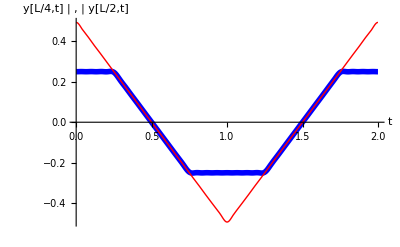

```mathematica
Plot[{y[L/4,t],y[L/2,t]},{t,0,2c/L},PlotStyle->{{Blue,Thickness[0.01]},Red},AxesLabel->{"t",Grid[{{Style["y[L/4,t]",FontColor->Blue, FontWeight->"Bold"],",",Style["y[L/2,t]",FontColor->Red]}}]}]
```

The center of the string oscillates back and forth in a triangle wave (thin line). The point at x=L/4 only starts to move after a certain period of time (thick line), which is required by the fact that waves have a finite propagation speed on the string. Recall that our initial condition is formed by pulling on the center of the string, holding it off axis against the string tension, and then releasing the string. Once the center has been released, it takes some time for this information to propagate to points far from the center. We will soon show that the speed of propagation of this signal is c. Thus, the point at L/4 does not learn that the point at L/2 has been released until time t=L/(4c) has elapsed. Only after this time does the point at L/4 begin to move.

#### 2. Example 2: Travelling Disturbance

The finite propagation speed of travelling disturbances can be easily seen directly by considering a different initial condition, which is localized in the middle of the string:

y_o(x)=ⅇ^(-50(x/L-1/2)^2),
v_o(x) = 0.

The resulting Fourier series solution will still have the form of Eq. (3.1.25) but the coefficients  A_n will be different. Now,  it is best to simply solve for these coefficients numerically:

```mathematica
L = 1; 
A[n_] :=2/L( NIntegrate[ ⅇ^(-50(x/L-1/2)^2) Sin[n Pi x/L],{x,0,L}] )
```

In Cell 3.6, we show the string motion resulting from this initial condition. (In order to reduce the computation time we have used the fact that only odd Fourier modes are present in the solution.)

```mathematica
M=19;c=1;
y[x_,t_] = Sum[A[n] Cos[n Pi c t/L] Sin[n Pi x/L],{n,1,M,2}];
ListAnimate[Table[Plot[y[x,t],{x,0,L},PlotRange->{{0,1},{-1,1}},PlotLabel->"t = "<>ToString[t],AxesLabel->{"x","y"}],{t,0,1.95,.05}]]
```

One can see that this initial condition breaks into two equal pulses, propagating in opposite directions on the string. This is expected from the left-right symmetry of the system: there is no reason why propagation of the pulse in one direction should be favored over the other direction. Also, the pulses do not change their shape until they reach the ends of the string, where they reflect and propagate back toward the center again, with opposite sign at time t=1. This means that each pulse, having covered a distance L=1 in time t=1, has traveled with speed c=1.

In fact,  it is easy to see that any function of space and time of the form f(x-c t) or f(x+c t) satisfies the wave equation for a uniform string, Eq. (3.1.10). This is because, for such functions, the chain rule implies that ∂f/∂t=±c∂f/∂x. Therefore,   ∂^2 f/∂t^2=c^2∂f/∂x^2, so f(x±c t) satisfies the wave equation for any function f.

In Chapter 5 we  will prove that  the general solution to the wave equation for a uniform infinite string can be written as a superposition of two such functions, traveling in opposite directions:

y(x,t)=f(x-c t)+g(x+c t).

This form of the solution is called  d'Alembert's solution, after its discoverer.

Disturbances of the form f(x±c t) travel with speed c  without changing shape. For example, if f(x) has a maximum at x=0, then this maximum point moves in time according to x=±c t. Every other point in the solution moves at the same speed, so the pulse does not change shape as it propagates. This is what we observed in Cell 3.6, up to the time that the pulses encountered the string ends.

## Static Sources and Inhomogeneous Boundary Conditions

#### Dirichlet and Neumann Boundary Conditions, and Static Transverse Forces

In the previous wave equation examples, the boundary conditions  y(0,t)=y(L,t)=0 were not of the most general type that can be handled using separation of variables. The ends of the string need not be fixed at the same height. The boundary conditions are then

y(0,t) = y_1 and y(L,t) = y_2.

Boundary conditions of this sort, where the value of the unknown function is specified at the end points, are referred to as Dirichlet boundary conditions, or boundary conditions of the first kind. We will now consider the solution of the wave equation for these Dirichlet boundary conditions, assuming that the boundary conditions are fixed in time; so that y_1 and y_2 are constants. Time-dependent boundary conditions cannot be handled using the separation-of-variables method discussed here, and will be left to Chapter 4.

However, other types of static boundary conditions can  be treated with separation of variables methods.  For instance, the derivative  ∂y/∂x, rather than x itself, can be specified at the ends of the string. This type of boundary condition is called a Neumann boundary condition. Such boundary conditions  do not often occur for problems involving waves on a string, because the string tension is usually created by fixing the string ends to posts. Therefore, in this section we will limit discussion to Dirichlet boundary conditions. On the other hand, Neumann boundary conditions can occur in other physical applications of the wave equation (see the exercises), and they also occur in applications involving other PDEs (see Sec. 3.1.3).

As a second generalization of the wave equation,  we note that for any earthbound string the force of gravity acts in the vertical direction, causing a horizontal string to sag under its own weight. This effect of gravity has been neglected so far, but can be incorporated into the wave equation as a source term (provided that the sag is small). To account for gravity or any other transverse external force, it is necessary to refer back to Fig. 3.3. An extra force of magnitude ⅆF now acts on the mass element in the y-direction. (For gravity, ⅆF=-ⅆm g.) This force must be added to the force acting to accelerate the element, on the right-hand side of Equation (3.1.4), which now reads

ⅆm ∂^2/(∂t^2)y(x,t)=ⅆx∂/(∂x)T_y(x,t) + ⅆF.

Dividing through by ⅆm, substituting for the string tension via Eq. (3.1.6), and using Eq. (3.1.2), we obtain an inhomogeneous wave equation with a source term:

∂^2/(∂t^2)y(x,t)=1/(ρ(x))∂/(∂x)(T(x) ∂/(∂x)y(x,t))+S(x),

where the source term S(x)=ⅆF/ⅆm is the acceleration caused by the external transverse force. We assume that this external source is time-independent; time-dependent sources are treated in Chapter 4.

#### The Equilibrium Solution

As a first step to obtaining the full solution  to this problem, we will first consider a time-independent solution of Eq. (3.1.28), subject to the boundary conditions  y(0,t) = y_1 and y(L,t) = y_2. This is the equilibrium solution for the shape of the string, y= y_eq(x).  This function satisfies the time-independent wave equation:

1/(ρ(x))∂/(∂x)(T(x) ∂/(∂x)y_eq(x,t))=-S(x),   y_eq(0)=y_1,y_eq(L)=y_2.

The general solution to this ODE can be obtained by direct integration:

y_eq(x) = -∫_0^x ⅆx'(1/(T(x'))∫_0^x' S(x'') ρ(x'')ⅆ x'')+ C_1 + C_2 ∫_0^x ⅆ x' 1/(T(x')).

The integration constants C_1 and C_2 are determined by the boundary conditions:

C_1=y_1,    C_2=(y_2-y_1+∫_0^L ⅆ x' 1/(T(x'))∫_0^x' S(x'') ρ(x'')ⅆ x'')/(∫_0^L ⅆ x' 1/(T(x'))) .

For instance, let us suppose that we are dealing with a gravitational force, S(x) = -g, that the string is uniform so that ρ(x) = ρ=constant,  and that  T(x) is also approximately uniform, T(x)≃T=constant. (The latter will be true if the tension in the string is large, so that the sag in the string is small). Then Eq.  (3.1.30)  becomes

y_eq(x) = -(g ρ)/(2T)x(L-x)+ (y_2-y_1)/L x +y_1.

This parabolic sag in the string is the small-amplitude limit of the well-known catenary curve for a hanging cable. For the case of zero gravity, the string merely  forms a straight line between the end points. Equation (3.1.32) is valid provided that the maximum displacement of the string due to gravity, |y_max| = g ρ L^2/8 T, is small compared to L. This requires that the tension satisfy the inequality T>> g ρ L/8. For low string tension where this inequality is not satisfied, the sag is large and nonlinear terms in the wave equation must be kept.  [A discussion of the catenary curve can be found in nearly any book on engineering mathematics. See, for instance,  Zill and Cullen (2000).]

#### The Deviation From Equilibrium

Having dealt with static source terms and inhomogeneous boundary conditions, we now allowr time-dependence in the full solution by writing y(x,t) as a sum of the equilibrium solution, y_eq(x), and a deviation from equilibrium, Δy(x,t):

y(x,t) = y_eq(x) + Δy(x,t).

A  PDE  for Δy is obtained by substituting Eq. (3.1.33) into Eq. (3.1.28).  Since y_eq(x) already satisfies Eq. (3.1.28),  Δy satisfies the homogeneous wave equation with homogeneous  boundary conditions,

∂^2/(∂t^2)Δy(x,t)=1/(ρ(x))∂/(∂x)(T(x) ∂/(∂x)Δy(x,t)),

Δy(0,t)=Δy(L,t)=0.

Initial conditions for Δy are obtained by substituting Eq. (3.1.33) into Eq. (3.1.9):

Δy(x,0)=y_o(x)-y_eq(x),
(∂Δy)/(∂t)(x,0)=v_o(x).

For the case of a uniform string, we know how to solve for Δy(x,t) by using separation of variables and a Fourier series. We will deal with a nonuniform string in Chapter 4.

This analysis shows that the static applied force and the  inhomogeneous boundary conditions have no effect on the string normal modes, which are still given by Eqs. (3.1.18) and (3.1.19) for a uniform string. This is because of the linearity of the wave equation. Linearity allows the application of the superposition principle to the solution, so that we can separate the effect of the static force and inhomogeneous boundary conditions from the time-dependent response to an initial condition.

## Summary

In this subsection we derived the wave equation, and  learned how to apply the method of separation of variables to solve the equation,  for the case of a uniform string with a static source S(x) and time-independent Dirichlet boundary conditions, y(0,t)=y_1,  y(L,t)=y_2.

First, we determined the equilibrium shape of the string, y_eq(x), as the time-independent solution to the PDE.  Then, we found that the deviation from equilibrium Δy(x,t) satisfies the homogeneous wave equation (i.e. no sources) with homogeneous boundary conditions y(0,t)=y(L,t)=0.

Homogeneity of the equation and the boundary conditions allowed us to apply separation of variables to the problem. The solution for Δy could be written as a Fourier sine series in x with time-dependent Fourier coefficients. Each Fourier mode was found to be  a normal mode of oscillation  - an eigenmode that matched the homogeneous boundary conditions and that satisfied an associated eigenvalue problem.

Other linear PDEs with time-independent sources and boundary conditions can also be solved using the method of separation of variables. In the next section we consider one such PDE: the heat equation.

3.1.3 Derivation of the Heat Equation

## Heat Flux

In a material for which the temperature T (measured in kelvins)  is a function of position, the second law of thermodynamics requires that heat will flow from hot to cold regions so as to equalize the temperature.  The flow of heat energy is described by an energy flux Γ=(Γ_x,Γ_y Γ_z), with units of watts per square meter. This flux is a vector, with the direction giving the direction of the heat flow. In a time Δt, the amount of heat energy ΔE flowing through a surface of area A, oriented transverse to the direction of Γ,  is ΔE =  A Γ Δt.

Consider a piece of material in the form of a slab of thickness L  and of cross-sectional area A, with a temperature T(x) that varies only in the direction across the slab, the x-direction (see Fig. 3.4).  It is an experimental fact that this temperature gradient results in a heat flux in the x-direction that is proportional to the temperature gradient,

Γ_x=-κ(∂T)/(∂x) ,

where κ, the constant of proportionality, is the thermal conductivity of the material. This constant is an intrinsic property of  the material in question. For example, pure water at room temperature and atmospheric pressure has κ=0.59 W/(m K), but copper conducts heat much more rapidly, having a thermal conductivity of κ=400  W/(m K). A temperature gradient of 1K/m  in water leads to an energy flux of 0.59 W/m^2 in the direction opposite to the temperature gradient, but in copper the flux is 400 W/m^2 . Since the energy flows down the gradient, it acts to equalize the temperature.

Note that  although thermal conductivity varies from one material to the next, it must be nonnegative; otherwise heat energy would flow up the temperature gradient from cold to hot regions, in contradiction to the second law of thermodynamics.

Fig. 3.4 Heat flux Γ_xin a slab of material of area A and thickness L, caused by a temperature T(x) that varies in the x-direction.

## Energy conservation

When T=T(x), Eq. (3.1.37) implies that the energy flux  Γ_x in the x direction is generally also a function of position. This, in turn, implies that the energy content of the material changes with time as energy builds up in some locations and is lost to other locations. We will now examine this process in detail.

Fig. 3.5: Energy change of an element of material of width Δx due to a source S and due to heat flux Γ_x.

Consider the volume element ΔV = A Δx shown in Fig. 3.5. This element, located at position x,  has a time-varying thermal energy content  ϵ(x,t) ΔV, where ϵ is the energy density of the material (energy per unit volume). The heat flux leaving this element from the right side has magnitude Γ_x(x+Δx,t), but the flux entering the element on the left side has magnitude Γ_x(x,t). The difference in these fluxes results in energy gained or lost to the element, at a rate A [Γ_x(x,t) - Γ_x(x+Δx,t) ].  In addition, extra sources of heat such as chemical or nuclear reactions can be occurring within the slab, adding or removing heat energy from the volume element at the rate ΔV S(x,t), where S(x,t) represents a given source of heat energy per unit volume, with units of watts per cubic meter (i.e. it is the power density of the source). In a time ⅆt, the total energy change of the element, ⅆ(ϵ ΔV), is the sum of these two terms multiplied by ⅆt:

ⅆ(ϵ ΔV) = ⅆt A (Γ_x(x,t) - Γ_x(x+Δx,t) )+ⅆt  ΔVS(x,t) .

Taylor expansion of the heat flux implies that ⅆt A (Γ_x(x,t) - Γ_x(x+Δx,t) ) = -ⅆt A Δx ∂Γ_x/∂x =-ⅆt ΔV ∂Γ_x/∂x . Dividing by ⅆt ΔV, we obtain the continuity equation for the energy density,

(∂ϵ)/(∂t)=-(∂Γ_x)/(∂x)+S(x,t).

## The Heat and Diffusion Equations. Dirichlet, Neumann, and Mixed Boundary Conditions.

When combined with Eq. (3.1.37), Eq. (3.1.38) yields  the following  partial differential equation:

(∂ϵ)/(∂t)=∂/(∂x)(κ (∂T)/(∂x))+S(x,t).

This equation can be used to obtain a temperature evolution equation,  because we can connect the energy density to the temperature via the laws of thermodynamics.  A change in the thermal energy density of the material causes a change  in the temperature according to the relation

ⅆϵ = C ⅆT,

where C is the specific heat of the material. This constant, with units of joules per cubic meter per kelvin, is another intrinsic property of the material.  Like the thermal conductivity, the specific heat must be nonnegative. For water at room temperature and at constant atmospheric pressure, the specific heat is C=4.2 ×10^6J/(m^3 K) , meaning that 4.2 MJ of heat energy must be added to a cubic meter of water in order to raise its temperature by 1 K. [A typical hot tub contains a few cubic meters of water, so one can see that tens of megajoules of energy are required to heat it by several degrees. Fortunately, 1 MJ of energy costs only a few pennies (as of 2002).] The specific heat of copper is not very different from that of water, C=3.5 ×10^6Joules/(m^3 K) .

When we combine Eqs. (3.1.39) and (3.1.40), we arrive at the following partial differential equation for the temperature T(x,t):

C(x)  (∂T)/(∂t)=∂/(∂x)(κ(x)(∂T)/(∂x))+S(x,t).

Equation (3.1.41) is the heat equation in one spatial dimension. In writing it we have allowed for spatial variation in the material properties κ and C . This can occur in layered materials, for example. The equation simplifies when κ and C are independent of position:

(∂T)/(∂t)=χ(∂^2 T)/(∂x^2)+(S(x,t))/C,

where χ is the thermal diffusivity of the material, defined as

χ=κ/C.

The thermal diffusivity has units of m^2/s. For water, χ=1.4×10^-7m^2/s, and for copper, χ=1.1×10^-4m^2/s. Equation (3.1.42) is sometimes referred to as the diffusion equation.

The heat equation is a first-order PDE in time and so requires a single initial condition, specifying the initial temperature in the slab as a function of position:

T(x,0) = T_o(x).

The equation is second-order in space, and so requires two boundary conditions to specify the solution. The boundary conditions one employs depend on the circumstances. For example, in some experiments one might fix the temperature of the slab faces to be given functions of time, by putting the faces in good thermal contact with heat reservoirs at given temperatures T_1(t) and T_2(t):

T(0,t) = T_1(t)
T(L,t) = T_2(t).,

These Dirichlet boundary conditions are of the same type as those encountered previously for the wave equation.

On the other hand, one might instead insulate the faces of the slab, so that no heat flux can enter or leave the faces: Γ_x(0)=Γ_x(L)=0. More generally, one might specify the heat flux entering or leaving the faces to be some function of time. Then according to Eq. (3.1.37), the temperature gradient at the faces is specified:

(∂T)/(∂x)(0,t) = -(Γ_(x 1)(t))/κ,
(∂T)/(∂x)(L,t) = -(Γ_(x 2)(t))/κ,

where Γ_(x 1)(t) and Γ_(x 2)(t) are given functions of time, equaling zero if the faces are insulated. Boundary conditions where the gradient of the unknown function is specified are called Neumann boundary conditions, or boundary conditions of the second kind.

There can also be circumstances where the flux of heat lost or gained from the slab faces is proportional to the temperature of the faces: for example, the hotter the face, the faster the heat loss.  This leads to mixed boundary conditions at the faces:

κ(∂T)/(∂x)(0,t)=a [T(0,t)- T_1(t)] ,
κ (∂T)/(∂x)(L,t)=-b[T(L,t)- T_2(t)].

where a and b  are given (nonnegative) constants. The functions T_1(t) and T_2(t) are the temperatures of the exterior surroundings: only if the face is hotter than the surroundings is there a flux of heat out of the face. If a and b are very large, representing good thermal contact with the surroundings, then the temperature of the faces is pinned to that of the surroundings and the boundary conditions are of Dirichlet form, Eq. (3.1.45). On the other hand, if a and b are very small, then the faces are insulating and obey homogeneous Neumann conditions, ∂T/∂x=0 at x=0 and x=L.

Finally, there can be situations where one face has a different type of boundary condition than the other; for instance, one side of a slab might be insulated, while on the other side the temperature might be fixed. These possibilites are summarized in Table 3.1.

Table 3.1. Some Possible Boundary Conditions for the Heat Equation^a 


Dirichlet | T(0,t)=T_1(t)
Neumann | κ(∂T)/(∂x)(0,t) = -Γ_(x 1)(t)
mixed | κ(∂T)/(∂x)(0,t)=a [T(0,t)- T_1(t)]

^aAt one end,  x=0.

3.1.4 Solution of the Heat Equation Using Separation of Variables

## Introduction

The heat equation for a uniform medium, Eq. (3.1.41), can often be solved using the method of separation of variables. For this method to work, we require that an equilibrium solution T_eq(x) for the temperature exist. A necessary (but not sufficient) requirement for equilibrium is time-independent boundary conditions and a time-independent source function.

If  an equilibrium solution can be found, then this solution can be subtracted out, and the deviation from equilibrium, ΔT(x,t), can then be analyzed using separation of variables, just as for the wave equation. However, if an equilibrium solution does not exist, then other more general solution methods  must be applied. Such methods will be discussed in Sec. 4.2.

One might have expected that time-independent boundary conditions and a time-independent source would necessarily imply that an equilibrium solution for the temperature exists. However, this is not always the case, as we will now show.

## Static Boundary Conditions and a Static Source

#### The Equilibrium Solution

We  consider time-independent boundary conditions,  of either the Dirichlet, the Neumann, or the mixed form,  and a static source function, S=S(x). We will look for an equilibrium solution T_eq(x) that satisfies these boundary conditions, as well as the time-independent heat equation,

0=∂/(∂x)(κ(x)(∂T_eq)/(∂x))+S(x).

This equation has a general solution that can be found by direct integration:

T_eq(x) = -∫_0^x ⅆx'(1/(κ(x'))∫_0^x' S(x'') ⅆ x'')+ C_1 + C_2 ∫_0^x ⅆ x' 1/(κ(x')).

The constants C_1 and C_2 are chosen to match the boundary conditions. For example, for Dirichlet boundary conditions at each end, T(0,t)=T_1 and T(L,t)=T_2,  the solution mirrors the equilibrium solution to the wave equation:

C_1=T_1,   C_2=(T_2-T_1+∫_0^L ⅆ x' 1/(κ(x'))∫_0^x' S(x'') ⅆ x'')/(∫_0^L ⅆ x' 1/(κ(x'))).

Similarly, one can also find a unique equilibrium solution for  mixed boundary conditions at each end [Eq. (3.1.47) with T_1 and T_2 constants], although we will not write the solution here. In fact, one can always find a unique equilibrium solution for every possible combination of static boundary conditions at each end, except one: Neumann conditions at each end.

#### Constraint Condition on the Existence of an Equilibrium for Neumann Boundary Conditions

If we specify Neumann boundary conditions, then according to Eq. (3.1.49) the derivative of the equilibrium temperature at each end must satisfy the following two equations:

κ(0)(∂T_eq)/(∂x)(0,t)=-Γ_(x 1)= C_2,
κ(L)(∂T_eq)/(∂x)(L,t)= -Γ_(x 2)= C_2-∫_0^L S(x'') ⅆ x''.

However, these are two equations in only one unknown, C_2. [The constant C_1 disappeared when the derivative of Eq. (3.1.49) was taken] Therefore, a solution cannot necessarily be found to these equations.  This should not be completely surprising. After all, Eq. (3.1.48) is being solved as a boundary-value problem, and we know that a solution to boundary-value problems need not exist.

Subtracting Eqs. (3.1.50) from one another implies that the equations have a solution for C_2 only if the external heat fluxes Γ_(x 1) and Γ_(x 2)are related to the heat source S(x) through

Γ_(x 1)-Γ_(x 2)+∫_0^L S(x'') ⅆ x''=0.

If this equation is not satisfied, there is no equilibrium solution. The equation follows from the requirement that, in equilibrium, the overall energy content of the material must not change with time.  In a slab with cross-sectional area A, the total energy content is  E=A∫_0^L ϵⅆx, where ϵ is the energy density. Setting the time derivative of this expression equal to zero yields

ⅆE/ⅆt=0=A∫_0^L (∂ϵ)/(∂t)(x,t)ⅆx=A∫_0^L (-(∂Γ_x)/(∂x)+S(x,t))ⅆx,

where the second equality follows from energy conservation, Eq. (3.1.38).   Performing the integral over the heat flux using the fundamental theorem of calculus then leads to Eq. (3.1.51).

Equation (3.1.51) is easy to understand intuitively: Take the case of an insulated slab, with Γ_(x 1)=Γ_(x 2)=0 . Then for a temperature equilibrium to exist, there can be no net heat energy injected into the slab by the source:∫_0^L S(x'') ⅆ x''=0; otherwise the temperature must rise or fall as the overall energy content in the slab varies with time. Similarly, if Γ_(x 1)-Γ_(x 2)<0, then we are removing heat through the faces of the slab; and in equilibrium this energy must be replaced by the heat source S(x).

For Dirichlet or mixed boundary conditions, where the external heat fluxes Γ_(x 1)and Γ_(x 2) are not directly specified, the fluxes through the slab faces are free to vary until the equilibrium condition of Eq. (3.1.51) is achieved. However, for Neumann boundary conditions these fluxes are specified directly, and if they do not satisfy Eq. (3.1.51), the energy content of the slab will increase with time [if the left-hand side of Eq. (3.1.51) is greater than zero] or decrease with time [if it is less than zero], and no equilibrium will exist.  Conditions such as this cannot be treated using separation of variables. A solution to this problem can be found in Chapter 4.

#### Separation of Variables for the Deviation from Equilibrium

Let's assume that the static boundary conditions and the source are such that Eq, (3.1.51) is satisfied, so that an equilibrium solution to the heat equation exists.  We can then determine the evolution of T(x,t) from a general initial condition, T(x,0)=T_o(x), by following the prescription laid out for the wave equation.

We first subtract out the equilibrium, and follow the deviation from equilibrium, ΔT(x,t), where

T(x,t) = T_eq(x) + ΔT(x,t).

Substitution of this expression into the heat equation (3.1.41) and application of Eq. (3.1.48) implies that  ΔT(x,t) satisfies the homogeneous heat equation

C(x)  (∂ΔT)/(∂t)=∂/(∂x)(κ(x)(∂ΔT)/(∂x))

with homogeneous  boundary conditions, and  initial condition

ΔT(x,0) = T_o(x)-T_eq(x).

The boundary conditions are of the same type as the original equation, but are homogeneous.  Recall that homogeneous boundary conditions are such that a trivial solution ΔT=0 exists. For instance, if the original equation had Neumann conditions at one end and Dirichlet conditions at the other, T(0,t)=T_1, ∂T/∂x|_(x=L)=-Γ_(x 2)/κ; then ΔT would satisfy homogeneous conditions of the same type, ΔT(0,t)=0,∂ΔT/∂x|_(x=L)=0.

The boundary conditions for the temperature deviation ΔT are of the same type as the original boundary conditions for T, but are homogeneous. (This was the point of subtracting out the equilibrium solution.)  Separation of variables only works if we can write down a PDE for ΔT that is accompanied by homogeneous boundary conditions.

The solution of Eq. (3.1.53) for ΔT can again be obtained using the method of separation of variables. Here for simplicity we will only consider the case where κ and C are constants, so that Eq. (3.1.53) becomes the diffusion equation,

(∂ΔT)/(∂t)=χ(∂^2 ΔT)/(∂x^2)

We look for a solution of the form ΔT(x,t)= f(t) ψ(x). Substituting this expression into Eq. (3.1.55) and dividing by f(t) ψ(x) yields

1/(f(t))(∂f)/(∂t)=χ/(ψ(x))(∂^2 ψ)/(∂x^2),

which can be separated into two ODEs. The left-hand side is independent of x, and the right-hand side is independent of t. Therefore, Eq. (3.1.56) can only be satisfied if each side equals a constant, λ:

1/(f(t))(∂f)/(∂t)=λ,

χ/(ψ(x))(∂^2 ψ)/(∂x^2)=λ.

#### The Eigenvalue Problem

The separation constant λ and the functions ψ(x) are determined by the homogeneous boundary conditions. Let us assume Dirichlet boundary conditions, ψ(0)=ψ(L)=0. With these boundary conditions, Eq. (3.1.58) may be recognized as an eigenvalue problem; in fact, it is the identical eigenvalue problem encountered previously for the wave equation! The solution for the eigenmodes is, as before,

ψ(x) = D sin(n π x/L)

and

λ=λ_n=-χ (n π/L)^2, n=1,2,3,....

In addition, the solution of Eq. (3.1.57),

f(t) = A ⅇ^(λ t),

provides the time-dependent amplitude for each eigenmode. By forming a linear superposition of these solutions, we obtain the general solution to the heat equation for the temperature perturbation away from equilibrium:

ΔT(x,t) = ∑_(n=1)^∞ A_n ⅇ^(λ_n t) sin (n π x/L),

As in the wave equation solution, we have absorbed the constant D into the Fourier coefficients A_n. These coefficients are found by matching the initial condition, Eq. (3.1.54):

ΔT(x,0)=∑_(n=1)^∞ A_n sin (n π x/L)=T_o(x)-T_eq(x).

This is a Fourier sine series, so the A_n's are determined as

A_n=2/L∫_0^L [T_o(x)-T_eq(x)]sin(n π x/L)ⅆx

Equations (3.1.61) and (3.1.62) are the solution for the deviation from equilibrium for the case of Dirichlet boundary conditions in a uniform slab. The solution is again made up of a sum of eigenmodes with the same spatial form as those for the wave equation, shown in Cell 3.1. But now the amplitudes of the modes decay with time with rate |λ_n|, rather than oscillating as in the wave equation. The result is that ΔT→0 . Thus, the full solution for T, Eq. (3.1.48), approaches the equilibrium solution T_eq(x) in the long time limit. The time evolution of several of these eigenmodes is displayed in Cell 3.7.

```mathematica
L=1;χ=1;
λ[n_] = -χ(n Pi /L)^2 ;
p[n_,t_] := Plot[Exp[λ[n]t] Sin[n Pi x],{x,0,L},Ticks->False,PlotRange->{-1,1},PlotLabel->"n = "<>ToString[n]];
ListAnimate[Table[Grid[{{p[1,t],p[2,t],p[3,t],p[4,t]}},ItemSize->Scaled[0.2]],{t,0,0.25,.0125}]]
```

All of the modes approach zero amplitude as time progresses,  because the boundary conditions on the eigenmodes dictate that the temperature equals zero at the slab faces.  Thus, in equilibrium the temperature deviation ΔT is zero throughout the slab. The higher-order modes equilibrate more rapidly, because they have larger gradients and therefore larger heat fluxes according to Eq. (3.1.37).

#### Example

In this example, we will assume a point heat source of the form S(x)= δ(x-L/2). We consider a slab of material of unit width, L=1, with thermal diffusivity χ=1, and κ=1 as well. Initially,  the slab has a temperature distribution T(x,0)=T_o(x)=x^3, and the boundary conditions are T(0,t)=0, T(1,t)=1.

Then the equilibrium temperature distribution is given by  Eq. (3.1.49) with C_1 and C_2 chosen to match the boundary conditions,  T_eq(0)=0 and T_eq(L) = 1. After performing the required integrals, we obtain C_1=0, C_2=3/2, and

T_eq(x) = 3x/2  - (x-1/2) h(x-1/2),

where h is a Heaviside step function. This equilibrium temperature distribution is displayed in Cell 3.8:

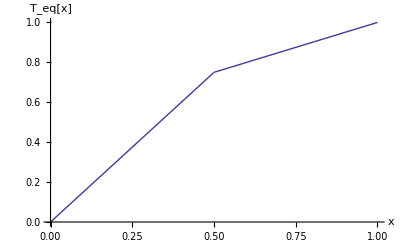

```mathematica
Teq[x_] =3x/2  - (x-1/2) UnitStep[x-1/2];
Plot[Teq[x],{x,0,1},AxesLabel->{"x","T_eq[x]"}]
```

The solution for the deviation from equilibrium,  ΔT(x,t),  is given by Eq. (3.1.61). The constants A_n are determined by the initial condition, T_o(x)=x^3, via Eqs. (3.1.62) and (3.1.63). The required integrals are performed using Mathematica and the behavior of T(x,t) is plotted in Cell 3.9, keeping 10 Fourier modes in the solution.

```mathematica
(*parameters*)
χ=L=1; M=20;
(* define the initial condition *)
T0[x_] = x^3;
(*determine the constants Subscript[A, n]*)
A[n_] := 2/L Integrate[Sin[n π x/L] (T0[x]-Teq[x]),{x,0,L}];
(*Fourier series for ΔT *)
ΔT[x_,t_] = Sum[A[n] Exp[-(n Pi/L)^2 χ t] Sin[n Pi x/L],{n,1,M}];
(*The full solution*)
T[x_,t_]=Teq[x] + ΔT[x,t];
(*Plot the result*)
ListAnimate[Table[Plot[T[x,t],{x,0,L},PlotRange->{{0,L},{0,1}},PlotLabel->"t = "<>ToString[t],AxesLabel->{"x","T"},PlotStyle->Thickness[0.01]],{t,0,0.4, 0.4/20}]]
```

[Note the text within the brackets (* *) , which is ignored by Mathematica. Comments such as these can be useful for documenting code.] The temperature  rapidly approaches the equilibrium temperature T_eq(x) as the point heat source raises the internal temperature of the slab.

Observe that the rate at which the equilibrium is approached is mainly determined by the lowest eigenmode. This is because the time dependence of the eigenmode amplitudes is given by  the factor ⅇ^(-χ (n π/L)^2 t). This factor decays rapidly for the modes with n>>1, so at large times the solution is approximately determined by the lowest mode:

T(x,t) ≃T_eq(x)+ A_1 ⅇ^(-χ (π/L)^2 t)sin (π x/L).

This equation implies that, for this problem, the maximum temperature deviation from equilibrium occurs at the center of the slab (x=L/2), and has the time dependence A_1 ⅇ^(-χ (π/L)^2 t), where A_1is determined from the initial condition by Eq. (3.1.62). Thus, at long times, the rate at which the slab temperature approaches  equilibrium is χ (π/L)^2. The larger the conductivity, the faster equilibrium is achieved. But the thicker the slab, the longer it takes for the heat to diffuse from the interior to the faces.

## Homogeneous Neumann Boundary Conditions

#### Separation-of-Variables Solution

Let us now consider the case of a uniform slab insulated on both sides, and with no source.  These conditions clearly satisfy Eq. (3.1.51), so an equilibrium exists- in this case the trivial equilibrium T_eq = constant. The temperature within the slab now evolves according to

(∂T)/(∂t)=χ(∂^2 T)/(∂x^2),

with homogeneous Neumann boundary conditions

(∂T)/(∂x)(0,t) = (∂T)/(∂x)(L,t) = 0

and initial condition

T(x,0) = T_o(x).

The solution of Eq. (3.1.65)  can again be obtained using the method of separation of variables. We now have no need to take out an equilibrium solution, since there is no source and the boundary conditions are already homogeneous. We look for a solution of the form T(x,t)= f(t) ψ(x). Substituting this expression into Eq. (3.1.65), and dividing by f(t) ψ(x), we have

1/(f(t))(∂f)/(∂t)=χ/(ψ(x))(∂^2 ψ)/(∂x^2),

which can be separated into two ODEs, Eqs. (3.1.57) and (3.1.58), just as before. We repeat these equations below:

1/(f(t))(∂f)/(∂t)=λ,

χ/(ψ(x))(∂^2 ψ)/(∂x^2)=λ,

#### The Eigenvalue Problem

The separation constant λ and the functions ψ(x) are determined by the homogeneous Neumann boundary conditions that ψ'(0)=ψ'(L)=0. These boundary conditions yield another eigenvalue problem: for all but a special set of λ-values, the only solution to Eq. (3.1.69) that satisfies these boundary conditions is the trivial solution  ψ=0.

To find the nontrivial solutions, we apply the boundary conditions to the general solution of Eq. (3.1.69), ψ(x)= C cos k x + D sin k x, with k=√(-λ/χ).  To match the condition that ψ'(0)=0, we require that D=0, and to match the condition that ψ'(L)=0, we find that either C=0 (the trivial solution) or k sin k x = 0. This equation can be satisfied with the choices k = n π/L, n=0,1,2,...., so we find that

ψ(x) = C cos(n π x/L)

and

λ=λ_n=-χ (n π/L)^2,    n=0,1,2,3,...

Forming a linear superposition of these solutions, we now obtain

T(x,t) = ∑_(n=0)^∞ A_n ⅇ^(λ_n t) cos (n π x/L),

where, as before, we absorb the constant C into the Fourier coefficients A_n. Note that we now keep the n=0 term  in the sum, since cos(0 π x) =1 is a perfectly good eigenmode.

Just as before, the coefficients A_n are found by matching the initial condition, Eq. (3.1.67):

T(x,0)=∑_(n=0)^∞ A_n cos(n π x/L)=T_o(x).

This is a Fourier cosine series, so the A_n's are determined as

A_n=2/L∫_0^L T_o(x)cos(n π x/L)ⅆx, n>0,

A_o=1/L∫_0^L T_o(x)ⅆx.

The solution is again made up of a sum of eigenmodes.  Although the eigenmodes differ from the previous case, they still form a set of orthogonal Fourier modes, which can be used to match  to the initial conditions.  Note that the n=0 eigenmode  has a zero eigenvalue, λ_o=0, so this mode does not decay with time. However, all of the higher-order modes do decay away. This has a simple physical interpretation: over time the initial temperature distribution simply becomes uniform within the slab, because the temperature equilibrates but heat cannot be conducted to the surroundings, due to the insulating boundary conditions.

#### Example

Let us assume that an insulated slab of unit width has an initial temperature equal  T_o(x) = x^2/16+x^3-(65 x^4)/32+x^5. This somewhat complicated initial condition is displayed in Cell 3.13. It is chosen so as to have a peak in the center, and zero derivatives at each end point.

The  Fourier coefficients A_n are determined  according to Eqs. (3.1.73).  The integrals are performed below, using Mathematica :

```mathematica
L=1;
T0[x_] = x^2/16+x^3-(65 x^4)/32+x^5;
A[n_] = (2/L)Integrate[T0[x] Cos[n Pi x],{x,0,L}] ;
A[0] = (1/L)Integrate[T0[x],{x,0,L}] ;
```

The forms for A_o and A_n are

```mathematica
A[0]
```

1/32

```mathematica
Simplify[A[n],n∈Integers]
```

-(3 (-160 (-1+(-1)^n)+(-8+23 (-1)^n) n^2 π^2))/(2 n^6 π^6)

This solution is shown in Cell 3.13, keeping M=20 terms in the sum over eigenmodes, and again taking χ=1.

```mathematica
(*parameters*)
χ=1;
M=20;
(* solution *)
T[x_,t_] =  Sum[A[n] ⅇ^(-(n Pi /L)^2 χ t)Cos[n Pi x],{n,0,M}];
(*Plot the result*)
ListAnimate[Table[Plot[T[x,t],{x,0,L},PlotRange->{{0,L},{0,.07}},PlotLabel->"t = "<>ToString[t],AxesLabel->{"x","T"}],{t,0,0.2, 0.2/20}]]
```

After a rapid period of relaxation, the n>0 modes in the initial condition decay away and the solution settles down to a uniform temperature distribution. Again, in the long-time limit, the higher-order eigenmodes die away and the solution is approximately

y(x,t) ≃A_o + A_1 ⅇ^(-χ (π/L)^2 t)cos(π x/L).

Now the maximum deviation from equilibrium occurs at the edges, as the temperature gradients within the insulated slab equilibrate.

## Homogeneous Mixed Boundary Conditions

Let us now turn to the case of no source and homogeneous mixed boundary conditions,

κ(∂T)/(∂x)(0,t)=a  T(0,t),
κ (∂T)/(∂x)(L,t)=-b T(L,t).

If we again apply separation of variables to the heat equation, writing  T(x,t) = f(t) ψ(x), we are again led to Eqs. (3.1.68) and (3.1.69) for the functions f and ψ. Equation (3.1.68) still has the general solution  f(t) = A ⅇ^(λ t), and  Eq. (3.1.69) is still an eigenvalue problem, with the general solution ψ(x) = A cos k x +B sin k x, where k=√(-λ/χ). But now the boundary conditions on ψ are rather complicated:

κ(∂ψ)/(∂x)(0)=a  ψ(0),
κ (∂ψ)/(∂x)(L)=-b ψ(L).

When these boundary conditions are used in the general solution  we obtain two coupled homogeneous equations for A and B:

κ k B  =a A,
κ k (-A sin k L+ B cos k L)=-b(A cos k L + B sin k L)

A nontrivial solution to these coupled equations exists only for values of k that satisfy

[ a b - κ^2 k^2] sin k L=-(a+b)κ k cos k L .

Again, we have an eigenvalue problem for the wavenumbers k. Unfortunately, this equation cannot be solved analytically  for k. However, numerical solutions can be found for specific values of a and b using the numerical techniques developed in Chapter 9. For example, if we take a=b=2κ/L, then Eq. (3.1.75) can be written as (4-s^2)sin s+4 s cos s=0, where s≡k L. The first four solutions for s can be found graphically as shown in Cell 3.14.

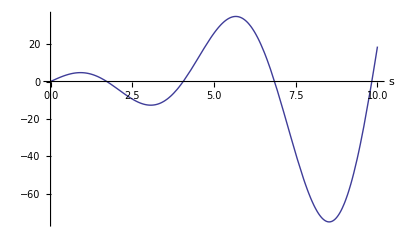

```mathematica
Plot[Sin[s ](-s^2+ 4)+4 s Cos[s],{s,0,10},AxesLabel->{"s",""}]
```

The plot shows that there are solutions at s≃1.7,4,7, and 9.5. The solution at s=0 is trivial, and those at s<0 provide modes that are merely opposite in sign to those with s>0. The corresponding λ-values can then be picked out using the following table of FindRoot commands:

```mathematica
Clear["Global`*"];
λ =-Table[s/.FindRoot[Sin[s ](-s^2+ 4)+4 s Cos[s],{s,1.8+2.5n}][[1]],{n,0,3}]^2χ/L^2
```

{-(2.9607 χ)/L^2,-(16.4634 χ)/L^2,-(46.9394 χ)/L^2,-(96.5574 χ)/L^2}

In Cell 3.16, we show the form of the corresponding  eigenmodes, taking A=1 and with B  given in terms of A by Eq (3.1.74). The time dependence ⅇ^(λ_n t) of the modes is also displayed.

```mathematica
L=1;χ=1;a=b=2 κ/L;
k=√(-λ/χ);
A=1;

B= a  A/(κ k );
ψ[n_,x_] :=  A Cos[√(-λ[[n]]/χ) x] + B[[n]] Sin[√(-λ[[n]]/χ) x];

p[n_,t_] := Plot[ Exp[λ[[n]]t] ψ[n,x],{x,0,L},Ticks->False,PlotRange->{-2,2},PlotLabel->"n = "<>ToString[n]];
ListAnimate[Table[Grid[{{p[1,t],p[2,t],p[3,t],p[4,t]}},ItemSize->Scaled[0.2]],{t,0,0.2,.01}]]
```

Because of the symmetry of the boundary conditions, the modes are either symmetric or antisymmetric about the center of the slab. These modes are a cross between insulating and fixed-temperature conditions: there is a small heat flux out of the slab faces that depends linearly on the temperature of the faces.  In the long-time limit, the temperature throughout the slab is zero in the absence of a heat  source.

We can still form a general superposition of these different solutions in order to satisfy the initial conditions:

T(x,t)=∑_n A_n ⅇ^(λ_n t)ψ_n(x),

where ψ_n(x) is the nth eigenmode, with corresponding eigenvalue λ_n. However, the eigenmodes are now complicated linear combinations of trigonometric functions, with wavenumbers that are no longer evenly spaced multiples of π/L. This is not a trigonometric Fourier series. How do we go about finding the constants A_n in this case?

Surprisingly, the eigenmodes are still orthogonal with  respect to one another:

∫_0^L ψ_m(x)ψ_n(x)ⅆx=0  if n≠ m.

One can check this numerically:

```mathematica
MatrixForm[Table[NIntegrate[ψ[n,x]ψ[m,x],{x,0,L},AccuracyGoal->10],{n,1,4},{m,1,4}]]
```

(1.85103 | 0. | 0. | -3.46945×10^-18
0. | 0.742963 | -1.04083×10^-16 | 0.
0. | -1.04083×10^-16 | 0.585216 | 3.81639×10^-17
-3.46945×10^-18 | 0. | 3.81639×10^-17 | 0.541426)

The off-diagonal elements in this table of integrals are nearly zero, indicating orthogonality of the eigenmodes within the precision of the numerical integration.

Since the modes are orthogonal, they can still be used to determine the A_n's  by matching to the initial conditions. At t=0, Eq. (3.1.76) implies

T(x,0) =∑_n A_n ψ_n(x)=T_o(x).

Multiplying both sides by ψ_m(x), and integrating over x from 0 to L, we obtain

∑_n A_n ∫_0^L ψ_m(x)ψ_n(x)ⅆx=∫_0^L ψ_m(x)T_o(x)ⅆx.

Orthogonality implies that each term in the sum vanishes except for the n=m term, so we find that only the n=m term survives, leaving a single equation for A_m:  A_m ∫_0^L ψ_m^2(x)ⅆx=∫_0^L ψ_m(x)T_o(x)ⅆx, which yields

A_m=∫_0^L ψ_m(x)T_o(x)ⅆx/∫_0^L ψ_m^2(x)ⅆx.

Equation (3.1.77) provides the coefficients A_m for every value of m. When used in Eq. (3.1.76), it yields the required solution T(x,t) for any given initial temperature T_o(x).

## Summary

In this subsection we found solutions to the heat equation using the method of separation of variables, the same approach as we employed when solving the wave equation. Just as for the wave equation, the approach only worked if we could find an equilibrium solution to the problem that took care of source terms and inhomogeneous boundary conditions. Then the deviation from equilibrium was  expanded as a series consisting of orthogonal eigenmodes with time-dependent amplitudes.

This was all completely analogous to the wave equation solution. However, we allowed for more general boundary conditions such as can often occur in heat equation problems. Along with the Dirichlet conditions familiar from the wave equation, we also considered Neumann and mixed conditions. These new boundary conditions brought with them several surprises.

First, we found that with static Neumann boundary conditions, an equilibrium solution for the temperature is not possible unless the temperature gradients at the edge of the system satisfy an energy conservation condition, Eq. (3.1.51).

Second, we found that in the case of mixed boundary conditions the eigenmodes used in our series solution for ΔT were not simple trigonometric Fourier modes. Surprisingly, however, the modes still formed an orthogonal set, which could be used to find a solution just as in a Fourier series expansion. We will discover the reason for this amazing "coincidence" in Chapter 4.

Exercises for Sec. 3.1

(1) A mass M hangs at the lower end of a vertical string, in equilibrium under the force of gravity g. The string has constant mass density ρ per unit length. The mass is at z=0, and the string is attached to the ceiling at z=L.  Find the tension T(z) in the string as a function of height z .

(2) A thin rod of height L is balanced vertically on its end at z=0. The rod has a nonuniform cross section. It is cylindrical, but has a radius that varies with height z as r= z/10. (That is, the rod is  a cone, balanced on its tip). The mass density of the material making up the cone is ℳ=1000 kg/m^3. Find the tension force in the rod vs. z (more aptly called compression force in this instance) due to gravity g .

(3) The following futuristic concept has been proposed for attaining orbit around a planetary body such as the earth: a very massive satellite, placed in geosynchronous orbit above the equator, lowers a thick rope (called a tether) all the way down to the ground. The mass of the satellite is assumed here for simplicity to be much larger than that of the tether. Astronauts, equipment, etc., simply ride an elevator up the tether until they are in space. Due the huge tension forces in the tether, only fantastically strong materials can be used in the design, such as futuristic materials made of carbon nanotubes.  Here, we will calculate the tension forces in the tether . [See also the article in the July-August 1997 issue of American Scientist on properties and uses of carbon nanotubes. The cover of this issue is reproduced in Fig. 3.6. (It depicts an open-ended tether design). Also, you may want to check out Sir Arthur Clarke's science fiction novel, The Fountains of Paradise.)

Fig. 3.6 Artist's depiction of a tether made of carbon nanotubes. Arist: D. M. Miller.

(a) Assuming that the mass density ρ per unit length of the tether is  constant, show that the tension T(r) as a function of distance r from the center of the earth is

T(r)=ρ W(r) + T_o,

where W(r)=-G M_e/r - ω^2 r^2/2 is the potential energy per unit tether mass, including potential energy associated with centrifugal force,  M_e is the mass of the earth, T_o is an integration constant that depends on the load tension at the base of the tether, and ω=2π/(24 hours). Evaluate and plot this tension versus  r, assuming that ρ=50 kg/m, that the tether is carrying no load, and that it is not attached to the earth at its base. What is the maximum value of the tension (in newtons) and where does it occur? (Hint 1: There are two competing forces at play on a mass element ⅆm in the tether: the centrifugal force due to the earth's rotation, ⅆm ω^2 r r̂, and the gravitational attraction of the tether to the earth -ⅆm G M_e r̂/r^2. Neglect the attraction of the tether to itself and to the massive satellite. Hint 2: For the massive satellite, recall that for a point mass m the radius R_g of geosynchronous orbit is given by the solution to the force balance equation G M_e m/R_g^2=m ω^2 R_g, where ω=2 π/(24 hours). Here, neglect the effect of the tether mass on the satellite orbit. Hint 3: Assuming that the tether is attached only to the satellite, not the earth,  the tension force applied to the tether by the satellite must  balance the total integrated centrifugal and gravitational forces on the tether.)

(b) The previous design is not optimized: the tension in the tether varies considerably with altitude, but the force F required to break the tether does not because the tether has uniform cross section. It is better to design a tether where the ratio of the breaking force to the tension is constant: F/T = S, where S is the safety factor, taken to be around 2 or 3 in many engineering designs.  Now, the breaking force F of the tether is proportional to its  cross-sectional area A, according to the equation F= τ A, where τ is the tensile strength of the material (in newtons per square meter). Also, the density per unit length, ρ, is given by ρ = ℳ A where ℳ is the mass density (in kilograms per cubic meter).

Find the cross-sectional area A(r) such that the safety factor S is constant with altitude. For a boundary condition, assume that there is a loading tension T_l applied at the base of the tether, at r=R_e, (R_e being the radius of the earth). Show that

A(r) = (S T_l)/τ ⅇ^(ℳS/τ[W(r)-W(R_e)]).

Plot  the radius of the tether, √(A(r)/π) (in meters), assuming that it is made out of the strongest and lightest commercially available material (as of the year 2000), Spectra (a high molecular-weight form of polyethylene), with a mass density of ℳ=970 kg/m^3 and a tensile strength of  τ=3.5×10^9 N/m^2. Take as the safety factor S=2.  Take T_l=10,000 Newtons. What is the total mass of this tether?

(c) Redo the calculation and plot of part b) for a tether made of carbon nanotubes. Take the same parameters as before, but a tensile strength 40 times greater than that of Spectra.

(4) Waves in shallow water:  Waves on the surface of water with long wavelength compared to the water depth are also described by the wave equation. In this problem you will derive the equation from first principles using the following method, analogous to that for a wave on a string. During the wave motion, a mass of fluid in an element of unit width into the paper, equilibrium height h and length Δx moves a distance η and assumes a new height h+z(x,t) and a length (1+ ∂η/∂x)Δx, but remains of unit width into the paper. (See Fig. 3.7.)

Fig. 3.7. A wave in shallow water, with motion greatly exaggerated.

(a) Using the incompressibility of the fluid (the volume of the element remains fixed during its motion) show that, to lowest approximation,

z=-h∂η/∂x.

(b) Neglecting surface tension, the net force in the x-direction on the element face of height h+z arises from the difference in hydrostatic pressure on each face of the element due to elements on the right and left of different heights. The hydrostatic pressure is a function of distance y from the bottom: p = ℳ g (h+z(x,t)-y), where ℳ is the mass density of the water and g is the acceleration of gravity. Show that the net force in the x-direction, ΔF_x, is given by

ΔF_x=-ℳ g h (∂z)/(∂x)Δx.

(c) Using the results from part (a) and (b), and Newton's 2nd law for the mass element,  show that shallow water waves satisfy the wave equation (∂^2 η)/(∂t^2)=c^2(∂^2 η)/(∂x^2), or alternately,

(∂^2 z)/(∂t^2)=c^2(∂^2 z)/(∂x^2).

where the wave speed c is given by

c=√(g h)

(d) A typical ocean depth is on the order of 4 km. Tidal waves have wavelengths that are considerably larger than this, and are therefore well described by the shallow-water wave equation. Calculate the wave speed (in kilometers per hour) for a tidal wave.

(5) In this problem we consider shallow-water waves, sloshing in the x-direction in a long channel of width L in the x-direction.  Boundary conditions on the waves  are that the horizontal fluid displacement in the x-direction, η (defined in the previous problem), equals zero at the channel boundaries (at x=0 and x=L).

(a) Find the eigenmodes and eigenfrequencies for η(x,t).

(b) Plot the wave height z vs x for the first three sloshing modes.

(6)(a) The high E -string of a steel string guitar is about L=0.7 m long.  It has a mass per unit length of ρ=5.3×10^-4 kg/m. Find the tension T required to properly tune the string, given that a high E has a frequency of  f = 1318.51 hertz.

(b) Assuming that the A string is under the same tension as the E string, is made of the same material,  and is about the same length, what is the ratio of the thickness of this string to that of the E string? An A tone has a frequency of  440 hertz.

(7) Using separation of variables, find the solution for the motion of a string that is governed by the following wave equation:

∂^2/(∂t^2)y(x,t)=∂^2/(∂x^2)y(x,t)+ f(x),

with boundary conditions y(0,t)=0=y(π,t), and initial conditions

(a) y(x,0)=x(π-x),   ∂/(∂t)y(x,0)=0. Take f(x)=0.

(b) y(x,0)=0,   ∂/(∂t)y(x,0)=x^2 sin x. Take f(x) = x.

(8) Transverse oscillations on a uniform string under uniform tension T and with mass density ρ need not be only in the y- direction - the oscillations can occur in any direction in a plane transverse to the equilibrium string. Call this plane the x-y plane, and the line of the equilibrium string the z-axis. Then, neglecting gravity effects,  a  displacement vector r(z,t)=(x(z,t),y(z,t)) of a mass element away from equilibrium satisfies the vector wave equation,

∂^2/(∂t^2)r(z,t)=c^2∂^2/(∂z^2)r(z,t).

(a) Find the spatial eigenmodes of this wave equation for boundary conditions r=0 at z=0 and z=L. Show that there are two independent plane polarizations for the eigenmodes: an eigenmode involving motion only in the y-direction,  and one only in the x-direction.

(b) Using the eigenmodes of part a) write down a solution r(z,t) for a rotating mode  with no nodes except at the ends (think of the motion of a skipping rope. ) (Hint: the x-motion is π/2 out of phase with the y motion.) Over one period, make an animation of the motion using ParametricPlot3D. This is an example of circular  polarization.

(9) A rope that is 2 L_1=12 meters long is attached to posts at x=±L_2that are at the same level, but are only 2 L_2=10 meters apart. Find and plot the equilibrium shape of the rope. (Hint: the element of length is

ⅆs=√(ⅆ x^2+ⅆ y^2)=ⅆx √(1+(ⅆy/ⅆx)^2)≈ⅆx [1+1/2(ⅆy/ⅆx)^2],

assuming small perturbations away from a straight rope. Use the linear wave equation to determine the equilibrium solution for y(x). [Answer to lowest order in (L_1-L_2)/L_1: y(x) =-(g ρ)/(2T)(L_2^2-x^2) where T= ρ g L_2 √(L_2/(6(L_1-L_2))) is the rope tension. ]

(10) A heavy string of length L and mass density ρ per unit length is spliced to a light string with equal length L and mass density ρ/4 per unit length. The combined string is fixed to posts and placed under tension T. The posts are both at the same height, so the string would be straight and horizontal if there were no gravity. Find and plot the shape of the string in the presence of gravity (assuming small displacement from horizontal). Take L=1 m, ρ=0.5 kg/m and T=25 N. Plot the shape.

(11) A mass of m=5 kg is attached to the center of a rope that has a length of 2 L_1=10 meters. The rope is attached to posts atx=±L_2that are at the same level but are only  2 L_2= 7 meters apart. The mass of the rope is M= 5 kg. Find the shape of the rope and the tension applied to the posts. [Use the linear wave equation to determine the equilibrium solution for y(x), assuming that |y|<<L_1.] Plot the shape. [Answer to lowest order in (L_1-L_2)/L_1:  y(x) =-g/(2T)(L_2-x)( m+M/2+ρ x), x>0, where T=  g  √((L_2(3 m^2+ 3 m M + M^2))/(24(L_1-L_2))) is the rope tension and ρ=M/2 L_1 is the mass density. ]

(12)(a) In the presence of gravity, the vector wave equation for a rope, Eq. (3.1.80), is modified to read

∂^2/(∂t^2)r(z,t)=c^2∂^2/(∂z^2)r(z,t)-g ŷ.

In equilibrium, the rope hangs with a parabolic shape given by Eq. (3.1.32). It is possible to oscillate the hanging rope back and forth like a pendulum. (Think of a footbridge swaying back and forth.) Find the frequency of this swaying motion, assuming that the length of the rope is L. (Hint: Apply the principle of superposition to take care of the source term, and determine the eigenmodes of the system.)

(b) If one assumes  that the rope oscillates like a rigid pendulum, show that the frequency of small oscillations  is √(10T/ρ L^2). (Recall that a pendulum has frequency √(τ/I), where τ is the maximum possible torque due to gravity and I is the moment of inertia about the pivot.) Why does this answer differ from the result of part a)?

(13) A quantum particle of mass m, moving in one dimension in a potential V(x),  is described by Schrödinger's equation,

ⅈ ℏ∂/(∂t)Ψ=Ĥ Ψ,

where Ψ(x,t) is the particle's wave function, the Hamiltonian operator Ĥ is given by

Ĥ=-ℏ^2/(2 m)∂^2/(∂x^2)+ V(x),

and  ℏ=1.055 ×10^-34 N m s is Planck's constant divided by 2π.
	 A quantum particle moves in a box of width L. Boundary conditions on the wave function are therefore ψ=0 at x=0 and x=L. Use separation of variables to solve the following initial-value problem: Ψ(0,x) = x^3(L-x). Animate the result for the probability density |Ψ|^2 over a time 0<t<20ℏ/m L^2.

(14) In a slab with uniform conductivity κ, find the equilibrium temperature distribution T_eq(x) under the listed conditions. Show directly that in each case Eq. (3.1.51) is satisfied.

(a) S(x)=S_o, T(0)=T_1,  T(L)=T_2.

(b) S(x)=x, (∂T)/(∂x)(0)=0,T(L)=0.

(c) S(x)= α δ(x-L/3),(∂T)/(∂x)(0)=T(0),(∂T)/(∂x)(L)=0  .

(15) The ceiling  of a Scottish castle consists of  1/4-meter-thick  material with thermal conductivity κ=0.5 W/(m K) Most of the heat is lost through the ceiling.  The exterior temperature is, on average,   0 °C, and the interior is kept at a chilly 15 °C. The surface area of the ceiling is 2000 m^2.  The cost per kilowatt-hour of heating power is 3 Pence. How much does it cost (in pounds) to heat the castle for one month (30 days)? (Note: One British pound equals 100 Pence.)

(16) Solve the following heat equation problem on 0<x<1, with given boundary and initial conditions, and plot the solution for 0<t<2 by making a table of plots at a sequence of 40 times:

(∂T(x,t))/(∂t)= (∂^2 T(x,t))/(∂x^2)+S(x).

Boundary conditions, initial conditions, and source:

(a)  T(0,t)=0, T(1,t)=3; initial condition T(x,0)=0, S(x)=0.

(b) Insulated at x=0, T(1,t)=1; initial condition T(x,0)= x, S(x)=1.

(c) Insulated on both faces, T(x,0)=0, S(x) = sin 2π x.

(17)(a) A slab of fat, thickness 2 cm, thermal diffusivity χ = 10^-6 m^2/s, and initially at temperature T=5 °C, is dropped into a pot of hot water at T=60°C. Find T(x,t) within the slab. Find the time t_o needed for the center of the fat to reach a temperature of 55°C. Animate the solution for T(x,t) up to this time.

(b) Over very long times, the behavior of T(x,t)is dominated by the eigenmode with the lowest decay rate. Keeping only this mode in the evolution, use this approximate solution for T to rederive t_o analytically, and compare the result with that found using the exact answer from part (a).

(18) A cold steak, initially at uniform temperature T(x,0)=8 °C, and of thickness L= 3 cm, is placed on a griddle (at x=0) at temperature T=250 °C. The steak will be cooked medium rare when its minimum internal temperature reaches T=65 °C.  How long does this take? Animate the solution for T(x,t) up to this time. (The boundary condition on the upper face of the meat at x=L can be taken to be approximately insulating. The thermal diffusivity of meat is about 3×10^-7 m^2/s. )

(19) A sheet of copper has thickness L , thermal diffusivity χ, and specific heat C.   It is heated uniformly with a constant power density S=j^2 ρ due to a current density j running through the sheet, where ρ is the resistivity of the copper. The faces of the sheet, each with area A and at temperature T_o (to be determined), radiate into free space with a heat flux given by the Stefan-Boltzmann law for black-body radiation: Γ=(1-r)σ T_o^4, where σ=5.67 ×10^-8 W/(m^2 K^4) is the Stefan -Boltzmann constant, and r is the reflectivity of the material, equal to zero for a blackbody and 1 for a perfect reflector.

(a) Find and plot the equilibrium temperature T_eq(x) in the sheet. What is the maximum temperature T_max as a function of the current density j?

(b) If the temperature varies by an amount ΔT(x,t) from equilibrium, the radiated power out of the face at x=0 changes by an amount

ΔΓ=(1-r){[T_o+ΔT(0,t) ]^4-T_o^4}≃4(1-r)σ T_o^3 ΔT(0,t)

(assuming that T_o >> ΔT), and similarly for the face at x=L.  Thus, the boundary condition for small temperature deviations is mixed. Find the first three eigenmodes and their rate of decay. Take L=1 cm, r=0.8, and S =10^3 W/m^3.

(20) Damped waves on a string of length π in gravity satisfy the wave equation
	 (∂^2 y)/(∂t^2)+ 1/4(∂y)/(∂t)=(∂^2 y)/(∂x^2)-1 ,  y(-π/2,t)=y(π/2,t)=0.
 For initial conditions y(x,0)=π/2-|x|, ẏ(x,0)=0,  plot y(x,t) for 0<t<20.

## 3.2 Laplace's Equation in Some Separable Geometries

In a region of space that is charge-free, the electrostatic potential ϕ(r)  satisfies Poisson's equation without sources:

∇^2 ϕ(r)=0,

where r=(x,y,z) is the position vector,  and the Laplacian operator ∇^2 is defined by

∇^2 =∂^2/(∂x^2)+∂^2/(∂y^2)+∂^2/(∂z^2).

This PDE is called Laplace's equation.  To solve for ϕ(r) within a specified volume V we require boundary conditions to be given on the surface S  of the volume (see Fig. 3.8). We will consider boundary conditions that fall into three categories:

Dirichlet, where ϕ|_S=ϕ_o(r)for some potential ϕ_o(r)applied to the surface S;

Neumann, where the directional derivative of ϕ normal to the surface is determined: n̂·∇ϕ|_S=E_o(r) where, n̂ is a unit vector perpendicular to the surface S, or

mixed, where (f ϕ+gn̂·∇ϕ)|_S=u_o(r) for some function u_o(r) and (nonnegative) functions f(r) and g(r)  . The functions f and g cannot both vanish at the same point on S.

These three boundary conditions are straightforward generalizations of the conditions of the same name, considered previously for one-dimensional PDEs. Physically, Dirichlet conditions can occur in the case where the surface S is a set of one or more conductors that are held at fixed potentials. Neumann conditions are less common in electrostatics problems, applying to the case where the normal component of the electric field is determined at the surface.  Mixed conditions rarely occur in electrostatics problems, but can sometimes be found in applications of Poisson's equation to other areas of physics, such as thermal physics [see Eq. (3.1.47), for example]

Fig. 3.8: Region V (unshaded). The surface of this region is S

3.2.1 Existence and Uniqueness of the Solution

For the above boundary conditions, can one always find a solution to Laplace's equation? And is this solution unique?

We will answer the second question first. If a solution exists, it is unique for Dirichlet or mixed boundary conditions. For Neumann boundary conditions, the solution is unique only up to an additive constant. This can be proven through the following argument.

Say that two solutions exist with the same  boundary conditions. Call these solutions ϕ_1 and ϕ_2. We will prove that these solutions must in fact be the same (up to an additive constant for Neumann boundary conditions).

The difference between the solutions, Φ = ϕ_1-ϕ_2, also satisfies the Laplace equation ∇^2 Φ=0, and has homogeneous  boundary conditions.  To find the solution to ∇^2 Φ=0 with homogeneous boundary conditions, multiply this equation by Φ and integrate over the volume of the domain. Then apply Green's first identity:

0=∫_V Φ∇^2 Φⅆ^3 r=∫_S Φ∇Φ·n̂ⅆ^2 r-∫_V ∇Φ·∇Φⅆ^3 r.

Now, for Dirichlet or Neumann boundary conditions, either Φ=0 or ∇Φ·n̂=0 on S, so the surface integral vanishes, and we are left with ∫_V (|∇Φ|)^2 ⅆ^3 r=0. Furthermore, since (|∇Φ|)^2 is always nonnegative, the only way this integral can be zero is if ∇Φ=0 throughout the domain. Therefore, Φ=constant  is the only solution. This implies that Φ=0 for Dirichlet boundary conditions, because Φ=0 on S; but for Neumann conditions, Φ=constant satisfies the boundary conditions.

For mixed boundary conditions,  Φ satisfies (f Φ+gn̂·∇Φ)|_S=0. Assuming that f(r) is nonzero over the some part of the surface S ( call this portion S_1), and g(r) is nonzero over the remainder of the surface (call it S_1^c ), Greens  first identity becomes

0=-∫_S_1 g/f(∇Φ·n̂)^2 ⅆ^2 r-∫_(S_1^c)  f/g(Φ)^2 ⅆ^2 r-∫_V ∇Φ·∇Φⅆ^3 r.
Each integral is nonnegative (since both f and g are nonnegative by assumption), and therefore by the same argument as before the only possible solution is Φ=0.

Therefore,  ϕ_1 and ϕ_2 are equal for Dirichlet or mixed boundary conditions, and for Neumann conditions  they differ at most by a constant. We have shown that the solution to the Laplace equation is unique  for Dirichlet and mixed conditions, and unique up to an additive constant for Neumann conditions.

One can also show that for Dirichlet and mixed boundary conditions, a solution can always be found. (We will later prove this by construction of the solution). For Neumann boundary conditions, however, a solution for the potential ϕ(r) only exists provided that the boundary conditions satisfy the following integral constraint:

∫_S ∇ϕ·n̂ⅆ^2 r=0.

This constraint on the normal derivative of the potential  at the domain surface follows from Laplace's equation through an application of  the divergence  theorem : 0=∫_V ∇^2 ϕⅆ^3 r=∫_S ∇ϕ·n̂ⅆ^2 r.

Students with some training in electrostatics will recognize Eq. (3.2.3) as a special case of Gauss's law, which states that the integral of the normal component to the electric field  over a closed surface must equal the charge enclosed in the surface (which in this case is zero).

If Eq. (3.2.3) is not satisfied, then there is no solution.  This only constrains Neumann boundary conditions, since only Neumann  conditions directly specify the normal derivative of ϕ.  For Dirichlet and mixed conditions, which do not directly specify ∇ϕ·n̂, one can always find a solution that satisfies Eq. (3.2.3).

We now consider several geometries  where the solution to Laplace's equation can be found analytically, using the method of separation of variables.

3.2.2 Rectangular Geometry

## General Solution

In rectangular coordinates (x,y),  a solution to Laplace's equation for ϕ(x,y) can be found using separation of variables. Following the by now familiar argument, we write

ϕ(x,y)=X(x)Y(y)

for some functions X and Y. If we substitute Eq. (3.2.4)  into the Laplace equation and divide the result by ϕ, we obtain

1/(X(x))(ⅆ^2 X)/(ⅆ x^2)+1/(Y(y))(ⅆ^2 Y)/(ⅆ y^2)=0.

As usual, this equation can be separated into two ODEs, one for  X and the other for Y:

1/(X(x))(ⅆ^2 X)/(ⅆ x^2)=λ,
1/(Y(y))(ⅆ^2 Y)/(ⅆ y^2)=-λ,

where λ is the separation constant. The general solution to each ODE can be found easily:

X(x)=C_1 ⅇ^(√λ x)+C_2 ⅇ^(-√λx),
Y(y)=C_3 ⅇ^(ⅈ √λ y)+C_4 ⅇ^(-ⅈ √λ y).

## Example 1: Dirichlet Boundary Conditions

The general solution given by Eq. (3.2.6) is useful for  boundary conditions specified on a rectangle, as shown in Fig. 3.9.

Fig. 3.9

The potential on the sides of the rectangle is specified by the four functions ϕ_A(y), ϕ_B(x), ϕ_C(y), and ϕ_D(x).

We first consider the special case where only ϕ_A(y) is nonzero.  Then the homogeneous boundary conditions on the bottom and the top imply that Y(0)=Y(b)=0.  We again confront an eigenvalue problem for Y(y). The condition Y(0)=0 implies that C_4=-C_3 in Eq. (3.2.6), so that Y(y) = 2 ⅈ C_3 sin √λ y. The condition that Y(L)=0 then implies that either C_3=0 (trivial) or √λ b=n π. Thus, we find that

Y(y) = D sin n π y/b,

where

λ=λ_n= (n π/b)^2, n = 1,2,3,..

Since there are many solutions, we can superimpose them in order to match boundary conditions on the other two sides:

ϕ(x,y)=∑_n (C_(1n) ⅇ^(n π x/b)+C_(2n) ⅇ^(-n π x/b))sin (n π y/b),

where, as usual, we have absorbed the constant D into the constants C_(1n) and C_(2n).

Equation (3.2.9) has an oscillatory form in the y-direction, and an exponential  form in the x-direction.   This is because Laplace's equation implies that ∂^2 ϕ/∂x^2=-∂^2 ϕ/∂y^2.  Therefore, a solution that oscillates sinusoidally in y, satisfying ∂^2 ϕ/∂y^2=-λ_n  ϕ, must be exponential in x.  By the same token, one can also construct a solution that consists of sinusoids in x and exponentials in y. That solution does not match the given boundary conditions in this problem, but is required for other boundary conditions such as those for which ϕ_A=ϕ_C=0.

To find the constants C_(1n) and C_(2 n), we now satisfy the remaining two boundary conditions. The potential is zero along the boundary specified by x=0, which requires that we take C_(2 n)=-C_(1 n) in Eq. (3.2.9). We then obtain

ϕ(x,y)=∑_n A_n sinh(n π x/b) sin (n π y/b),

where A_n=2 C_(1 n).   The constants A_n in Eq. (3.2.10)  are determined by the boundary condition that ϕ(a,y)=ϕ_A(y):

ϕ_A(y)=∑_(n=1)^∞ A_n sinh (n π a/b)sin(n π y/b).

Equation (3.2.11) is a Fourier sine series for the function ϕ_A(y) defined on 0<y<b. The Fourier coefficient A_n sinh (n π a/b) is then determined by Eq. (2.2.11),

A_n sinh (n π a/b)=2/b∫_0^b ϕ_A(y)sin(n π y/b)ⅆy.

Equations (3.2.10) and (3.2.12) provide the solution for the potential within a rectangular enclosure for which the potential is zero on three sides, and equals ϕ_A(y) on the fourth side. 
	For instance, if ϕ_A(y) = sin (n π y/b), then the solution for ϕ(x,y) consists of only a single term,

ϕ(x,y) = (sinh(n π x/b))/(sinh(n π a/b)) sin(n π y/b).

This solution is plotted in Cell 3.18 for the case n=3 and a=b=1.

```mathematica
a=b=1; n=3;
ϕ[x_,y_] =Sinh[n Pi x/b]/Sinh[n Pi a/b] Sin[n Pi y/b];

Plot3D[ϕ[x,y],{x,0,a},{y,0,b},PlotLabel->"Potential in a box",AxesLabel->{"x","y",""},PlotRange->All,PlotPoints->30]
```

-Graphics3D-

The reader is invited to vary the value of n in this solution, as well as the shape of the box.

We can use this solution method to determine the general solution for the case of arbitrary nonzero potentials specified on all four sides at once by using the following argument. We can  repeat our analysis, taking the case where ϕ_A=ϕ_C=ϕ_D=0 and only ϕ_B(x) is nonzero, next evaluating the case where ϕ_A=ϕ_B=ϕ_D=0 and ϕ_C(y) is nonzero, and finally taking the case where ϕ_A=ϕ_B=ϕ_C=0 and ϕ_D(x) is nonzero. We can then superimpose the results from these calculatiosn to obtain the potential ϕ(x,y) for any combination of potentials specified on the rectangular boundary.

## Example 2: Neumann Boundary Conditions; the Current Density in a Conducting Wire

Let's now study an example with Neumann boundary conditions over part of the surface. Consider a current-carrying wire made of electrically conductive material, such as copper (see Fig. 3.10) The length of the wire is b, and its width is a . (For simplicity, we neglect any z-dependence.) The left and right sides of the wire are insulated (coated with rubber, say). To the top of the wire, a voltage V_o is applied, causing a current I (in amperes) to run through to the bottom, where is it extracted (see the figure). The question is to determine the distribution of current and the electric field inside the wire.

These two quantities are related: current flows because there is an electric field E=-∇ϕ inside the conductor. The current density j inside the rod (in amperes per square meter) satisfies Ohm's law, j = σ E, where σ is the electrical conductivity of the material. We wish to determine j(x,y) and E(x,y) [or equivalently, ϕ(x,y)].

Fig. 3.10 Current density in a wire

The boundary conditions on the top and bottom faces of the wire are set by the applied potentials:

ϕ(x,0)=0,
		ϕ(x,b)=V_o.

However, the boundary conditions on the two insulated sides are determined by the fact that no current flows through these sides, so the current runs parallel to these faces. Therefore, according to Ohm's law, j_x=σ E_x=-σ(∂ϕ)/(∂x)=0 along these faces, so we have Neumann conditions on these faces:

(∂ϕ)/(∂x)(0,y)=(∂ϕ)/(∂x)(a,y)=0

Furthermore, the potential in the interior of the conductor must satisfy Laplace's equation. This is because there are no sources or sinks of current in the interior of the rod, so ∇·j=0 [recall the discussion surrounding Eq. (1.2.12)]. Then Ohm's law implies

∇·σE=-σ ∇^2 ϕ=0.

We can now solve this Laplace's equation for the potential, using separation of variables. Given the boundary conditions of Eq. (3.2.13),  we expect from our standard separation-of-variables argument that ϕ(x,y) will consist of a sum of terms of the form Y(y) X(x), with X(x)  being an eigenmode of the Neumann form,  X(x) = cos(n π x/a), n=0,1,2,....  Substitution of this form into ∇^2 ϕ=0 then implies that Y(y) satisfies

(ⅆ^2 Y)/(ⅆ y^2)-((n π)/a)^2 Y=0.

For n>0 the solution that is zero at y=0 is Y(y)= A_n sinh(n π y/a). However, we must be careful; the n=0 term must also be kept. For n=0 the solution that is zero at y=0 is Y(y)=A_o y. Therefore, the potential has the form

ϕ(x,y)=∑_(n=1)^∞ A_n sinh (n π y/a) cos(n π x/a) + A_o y.

This solution matches the boundary conditions on the bottom and sides. The constants A_n are then determined by satisfying the boundary condition on the top face, V_o =∑_(n=1)^∞ A_n sinh (n π b/a) cos(n π x/a) + A_o b. This is simply a Fourier cosine series in x. The Fourier coefficients are A_o = V_o/b and

A_n = (2 V_o)/(a sinh(n π b/a))∫_0^a cos(n π x/a)ⅆx, n>0.

However, the integral over the cosine  equals zero, so the only nonzero Fourier coefficient is A_o = V_o/b. Therefore, the solution for the potential interior to the wire  is simply ϕ(x,y)=V_o y/b. The electric field in the wire is uniform, of magnitude V_o/b. The current density runs vertically and uniformly throughout the conductor, with magnitude j=σ V_o/b.

3.2.3 2D Cylindrical Geometry

## Separation of Variables

The general solution to Laplace's equation can also be found in cylindrical geometry (r, θ,z). The cylindrical radius r and the angle θ are defined by the coordinate transformation x=r cosθ and y=r sinθ. At first, for simplicity, we consider the case where the potential is independent of z, so that  ϕ=ϕ(r,θ).  In these 2D cylindrical coordinates, the method of separation of variables can again be used to solve Laplace's equation. We assume that the potential takes the form

ϕ(r,θ) = R(r) Θ(θ).

In cylindrical coordinates ∇^2  is given by

∇^2 = 1/r∂/(∂r)(r∂/(∂r))+1/r^2∂^2/(∂θ^2)+∂^2/(∂z^2).

Applying ∇^2  to Eq. (3.2.15) and dividing by  R(r) Θ(θ) yields

1/(r R(r))∂/(∂r)(r(∂R)/(∂r))+1/(r^2 Θ(θ))(∂^2 Θ)/(∂θ^2)=0.

Following the standard procedure, this equation can be separated into two equations for the r and θ dependence. The expression 1/(Θ(θ))(∂^2 Θ)/(∂θ^2) must equal some function of θ, which we call f(θ). Equation (3.2.17) can then be written as

1/(r R(r))∂/(∂r)(r(∂R)/(∂r))+(f(θ))/r^2=0.

However, as the rest of the equation is independent of θ, it can only be satisfied if f(θ) is a constant, f(θ)=-m^2 (where we have anticipated that the constant will be nonpositive). Then the equation for Θ(θ) is

(∂^2 Θ)/(∂θ^2)=-m^2 Θ(θ).

The boundary conditions on this equation arise from the fact that the variable θ is periodic: the angles  θ+2π and θ are equivalent. This implies that we must require periodic boundary conditions, Θ(θ+2π)=Θ(θ).  With these boundary conditions, we again have an eigenvalue problem, because these boundary conditions allow only the trivial solution Θ(θ)=0, except for special values of m. These values may be found by examining the general solution to Eq. (3.2.19),

Θ(θ)=A ⅇ^(ⅈ m θ)+ B ⅇ^(-ⅈ m θ).

For nonzero A and B, the periodic boundary conditions imply that ⅇ^(±ⅈ m θ)=ⅇ^(±ⅈ m (θ +2π)), which requires that ⅇ^(±ⅈ  2π m)=1. This can only be satisfied if m is an integer. Therefore, we obtain

Θ(θ) = ⅇ^(ⅈ m θ), m ∈ Integers

[Allowing m to run over both positive and negative integers accommodates both independent solutions in Eq. (3.2.20).]

Turning to the radial equation, we find that  for f(θ)= -m^2, Eq. (3.2.18) becomes

1/r∂/(∂r)(r(∂R)/(∂r))-m^2/r^2 R(r) = 0.

This equation has the following general solution,

R(r) ={A_m  r^(|m|) + B_m /r^(|m|),   m≠ 0,
A_o  + B_o  ln r,               m=0.

The general solution to the Laplace equation in cylindrical coordinates is a sum of these independent solutions:

ϕ(r,θ)=A_o  + B_o ln r+ ∑_(m=-∞
m≠ 0)^∞ (A_m r^(|m|)+B_m/r^(|m|))ⅇ^(ⅈ m θ) .

## Example

The general solution to Laplace's equation in cylindrical coordinates is useful when boundary conditions are provided on the surface of a cylinder or cylinders. For instance, say the potential is specified on a  cylinder of radius a :

ϕ(a,θ)=V_a(θ).

We require a solution to Laplace's equation in 0 ≤ r≤ a. This solution is given by Eq. (3.2.24); we only need to match the boundary conditions to determine the constants A_n and B_n. First, the fact that the potential must be finite at r=0 implies that B_n=0 for all n. Next, Eqs. (3.2.24) and (3.2.25) imply that

Σ_(m=-∞)^∞A_m a^(|m|)ⅇ^(ⅈ m θ)=V_a(θ),

This is an exponential Fourier series, so  the Fourier coefficients can be determined using Eq. (2.2.3) :

A_m a^(|m|)=1/(2 π)∫_0^(2 π) V_a(θ)ⅇ^(-ⅈ m θ)ⅆθ.

The solution for the potential is 
		ϕ(r,θ) =Σ_(m=-∞)^∞A_m r^(|m|)ⅇ^(ⅈ m θ) .

For instance, if V_a(θ) = V_o sin θ, then only the m=±1  terms in the sum contribute to the solution, and the rest are zero. This is because sin θ contains only m=±1 Fourier components.  The solution is then clearly of the form ϕ(r,θ) = A r sin θ, and the constant A can be determined by matching the boundary condition that V(a,θ) =V_o sin θ . The result is

ϕ(r,θ) = V_o r/a sin θ.

3.2.4 Spherical Geometry

## Separation of Variables

We next consider the solution to Laplace's equation written in spherical coordinates (r,θ,ϕ). These coordinates are defined by  the transformation x=r sin θ cosϕ, y=r sin θ sinϕ, and z=r cosθ (see Fig. 3.11) . In these coordinates Laplace's equation becomes

∇^2 Ψ=1/r^2∂/(∂r)(r^2(∂Ψ)/(∂r))+1/(r^2 sinθ)∂/(∂θ)(sinθ(∂Ψ)/(∂θ))+1/(r^2 sin^2 θ)(∂^2 Ψ)/(∂ϕ^2).

(We use the symbol Ψ  for potential in this section so as not to confuse it with the azimuthal angle ϕ.) We again employ  the method of separation of variables, writing

Ψ(r,θ,ϕ)=R(r)Θ(θ)Φ(ϕ).

Then the equation (∇^2 Ψ )/Ψ = 0 is

1/(r^2 R)∂/(∂r)(r^2(∂R)/(∂r))+1/(r^2 sinθ Θ)∂/(∂θ)(sinθ(∂Θ)/(∂θ))+1/(r^2 sin^2 θ Φ)(∂^2 Φ)/(∂ϕ^2)=0.

Fig. 3.11 Spherical coordinates (r,θ,ϕ).

The separation-of-variables analysis proceeds just as before. One finds that Eq (3.2.28) separates into three ODEs for R, Θ, and Φ:

(∂^2 Φ)/(∂ϕ^2)=-m^2Φ(ϕ),

1/sinθ∂/(∂θ)(sinθ(∂Θ)/(∂θ))-m^2/(sin^2 θ)Θ(θ)=λ Θ(θ),

1/r^2∂/(∂r)(r^2(∂R)/(∂r)) +λ/r^2 R(r)=0,

where we have  introduced the separation constants m and λ.  Just as in cylindrical coordinates, periodicity of the angle ϕ implies that m must be an integer, so that the eigenvalue problem posed by Eq. (3.2.29) has the solution

Φ(ϕ) = ⅇ^(ⅈ m ϕ), m∈ Integers.

## Eigenmodes in θ: Associated Legendre Functions

Turning to Eq. (3.2.30), we make a coordinate transformation to the variable x=cosθ. Then by the chain rule, (∂Θ)/(∂θ)=(∂x)/(∂θ)(∂Θ)/(∂x)=-sinθ (∂Θ)/(∂x)=-√(1-x^2)(∂Θ)/(∂x). When written in terms of x, Eq. (3.2.30)  becomes

∂/(∂x)((1-x^2)(∂Θ)/(∂x))-m^2/(1-x^2)Θ(x)=λ Θ(x)

This ODE has regular singular points at x=±1. Its general solution is in terms of special functions called hypergeometric functions. In general, these functions are singular at the end points because of the regular singular points there.  However, for special values of λ, the solution is finite at both ends. Again, we have an eigenvalue problem. In this case, the eigenvalues are

λ = -l(l+1)  for l a positive integer taking on the values  l≥ |m|.

The corresponding eigenmodes are special cases of the hypergeometric functions called associated Legendre functions,

Θ(θ)=P_l^m(x)   ,x=cos θ.

For m=0  the functions P_l^m(x) are simple polynomials called Legendre polynomials,  but for m≠ 0 , they have the form of a polynomial of order l-|m| multiplied by the factor (1-x^2)^(|m|/2). Some of these functions are listed in Table 3.2.

Table 3.2  Associated Legendre Functions P_l^m(x)
l | m=-2 | -1 | 0 | 1 | 2
0 | "" | "" | 1 | "" | ""
1 | "" | (√(1-x^2))/2 | x | -√(1-x^2) | ""
2 | 1/8 (1-x^2) | 1/2 x √(1-x^2) | -1/2+(3 x^2)/2 | -3 x √(1-x^2) | 3 (1-x^2)

The table shows, among other things,  that the functional form of P_l^m(x) differs only by a constant from P_l^-m(x).

We can see using Mathematica that the associated Legendre functions P_l^m(x) satisfy Eq. (3.2.33).  In Mathematica these functions are  called LegendreP[l,m,x]. The following cell tests whether each Legendre function satisfies Eq. (3.2.33) :

```mathematica
Θ[x_] = LegendreP[l,m,x];
FullSimplify[D[(1-x^2)Θ'[x],x] - m^2 Θ[x]/(1-x^2) == -l(l+1)Θ[x]]
```

True

Turning to the radial dependence of the potential, we require the solution of Eq. (3.2.31), with λ=-l(l+1):

```mathematica
Expand[FullSimplify[R[r]/.DSolve[1/r^2 D[ r^2  D[R[r],r],r]-l(l+1)R[r]/r^2==0,R[r],r][[1]],l≥ 0]]
```

r^l C[1]+r^(-1-l) C[2]

Thus,

R(r)=A/r^(l+1)+ B r^l,

where A and B are constants.

Since l and m can take on different values, we have actually found an infinite number of independent solutions to Laplace's equation. We can sum them  together to obtain the general solution in spherical coordinates:

Ψ(r,θ,ϕ)=∑_(l=0)^∞ ∑_(m=-l)^l (A_(l m)/r^(l+1)+ B_(l m) r^l)ⅇ^(ⅈ m ϕ)P_l^m(cos θ).

Finally, we are left with the task of determining the constants A_(l m) and B_(l m) in terms of the boundary conditions. Say, for example, we know the potential on the surface of a sphere of radius a to be Ψ(a,θ,ϕ) =V(θ,ϕ).  If we require the solution within the sphere, we must then set A_(l m)=0 in order to keep the solution finite at the origin. At r=a we have

∑_(l=0)^∞ ∑_(m=-l)^l B_(l m) a^l ⅇ^(ⅈ m ϕ)P_l^m(cos θ) =V(θ,ϕ) .

It would be useful if the associated Legendre functions formed an orthogonal set, so that we could determine the Fourier coefficients by extracting a single term from the sum.  Amazingly,  the associated Legendre functions do satisfy an orthogonality relation:

∫_0^π P_l^m(cos θ) P_(l̄)^m(cos θ)sin θⅆθ=2/(2l+1)((l+m)!)/((l-m)!)δ_(l,l̄).

Thus, we can determine B_(l m) by multiplying both sides of Eq. (3.2.36) by ⅇ^(-ⅈ m ϕ)P_l^m(cos θ), and then integrating over the surface of the sphere, (i.e., applying  ∫_0^π sinθ ⅆθ∫_0^(2π) ⅆϕ ). This causes all terms in the sum to vanish except one, providing us with an equation for B_(l m):

2 π 2/(2l+1)((l+m)!)/((l-m)!)B_(l m)a^l=∫_0^π sinθ ⅆθ∫_0^(2π) ⅆϕ  ⅇ^(-ⅈ m ϕ)P_l^m(cos θ)V(θ,ϕ),

where on the left-hand side we have used Eq. (3.2.37).

Again, we observe the surprising fact that the nontrigonometric eigenmodes P_l^m(cos θ) form an orthogonal set on the interval 0<θ<π, just like trigonometric Fourier modes, but with respect to the integral given in Eq. (3.2.37). The reasons for this will be discussed in Chapter 4.

## Spherical Harmonics

It is often convenient to combine the associated Legendre functions with the Fourier modes ⅇ^(ⅈ m ϕ). It is conventional to normalize the resulting functions of θ and ϕ, creating an orthonormal set called the spherical harmonics Y_(l,m)(θ,ϕ):

Y_(l,m)(θ,ϕ)=√((2l+1)/(4π)((l-m)!)/((l+m)!))P_l^m(cosθ)ⅇ^(ⅈ m ϕ).

Mathematica has already defined these functions, with the intrinsic function SphericalHarmonicY[l,m,θ,ϕ]. The spherical harmonics obey the following orthonormality condition with respect to an integral  over the surface of a unit sphere:

∫_0^(2π) ⅆϕ∫_0^π ⅆθ sinθ (Y_(l̄, m̄))^*  Y_(l, m) =δ_(l l̄)δ_(m m̄).

We have already seen in Eq. (3.2.38) that spherical harmonics are useful in decomposing functions defined on the surface of a sphere, f(θ,ϕ), such as the potential on a spherical conductor. The spherical harmonics also enter in many other problems with spherical symmetry. For instance, they describe some of the normal modes of oscillation of a rubber ball, and this example provides a useful method for visualizing the spherical harmonics.

The plots in Cell 3.21 show the distortion of the ball for the m=0 modes, and for l=0,...,5.  These modes are cylindrically-symmetric because they have m=0. In each case the dashed line is the unperturbed spherical surface of the ball. We then add to this surface a distortion proportional to the given spherical harmonic.

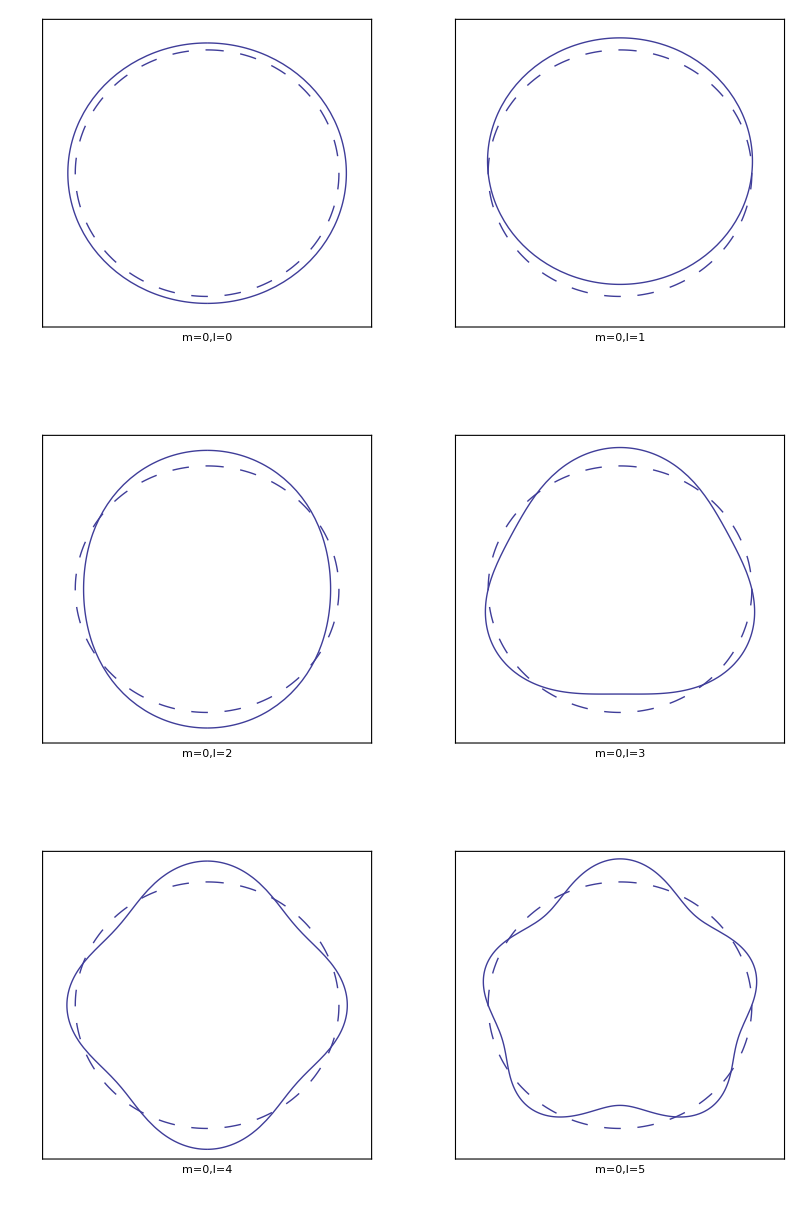

```mathematica
m=0; 
a=ParametricPlot[{Sin[θ],Cos[θ]},{θ,0,2Pi},PlotStyle->Dashing[{0.03,0.03}]];

r[θ_,ϕ_,l_]=1 + 0.2Re[SphericalHarmonicY[l,m,θ,ϕ]];
b[l_]:=ParametricPlot[r[θ,0,l]{Sin[θ]Cos[0],Cos[θ]},{θ,0,Pi}];
c[l_]:=ParametricPlot[r[θ,Pi,l]{Sin[θ]Cos[Pi],Cos[θ]},{θ,0,Pi}];
d[l_] := Show[a,b[l],c[l],PlotRange->{{-1.2,1.2},{-1.2,1.2}},AspectRatio->1,Frame->True,FrameTicks->False,FrameLabel->"m="<>ToString[m]<>",l="<>ToString[l],RotateLabel->False,AxesLabel->{"x","z"}];

   Show[GraphicsGrid[{{d[0],d[1]},{d[2],d[3]},{d[4],d[5]}}],PlotLabel->"m="<>ToString[m]<>" Spherical Harmonics"]
```

One can see that the l=0,m=0 harmonic corresponds to a spherically-symmetric expansion (or contraction) of the surface; the l=1,m=0 harmonic is a displacement of the sphere along the z-axis; the l=2,m=0 harmonic is an elliptical distortion of the surface; and higher-order harmonics correspond to more complicated distortions. The higher-order distortions have the appearance of sinusoidal oscillations along the surface of the sphere. As one travels from pole to pole along the sphere, the number of times each oscillation passes through zero equals l.

The m≠ 0 spherical harmonics are similar to the m=0 harmonics with the same l , except that the distortions are tilted away from the z-axis. For a given value of m, larger l corresponds to a smaller tilt. For l=|m|, the tilt is 90 °, that is, the maximum distortion is in the x-y plane. In Fig. 3.12 are some pictures of the real part of the m=1 modes. The reader is invited to modify the commands in Cell 3.21 and display other modes.

Fig. 3.12 m=1 Spherical harmonics

One can see that the l=1, m=±1 distortions correspond to displacements of the sphere in the x-y plane ; the l=2, m=±1 modes correspond to a tilted elliptical distortion. The distortion can be rotated about the z-axis through any angle ϕ_o by multiplying the spherical harmonic by a complex number ⅇ^(-ⅈ ϕ_o) before taking the real part. Three -dimensional visualizations of some of these modes can also be found in Sec. 3.3.3.

## Example

Consider a hollow conducting sphere where the upper half is grounded and the lower half is held at potential V_o:

V(θ,ϕ) ={V_o,   0 < θ<π/2,
0            otherwise.

The potential within the sphere is found by first dropping terms in Eq. (3.2.35)  proportional to 1/r^(l+1) :

Ψ(r,θ,ϕ)=∑_(l=0)^∞ ∑_(m=-l)^l B_(l m) r^l Y_(l, m)(θ,ϕ).

Matching this solution to  V(θ,ϕ), we obtain ∑_(l=0)^∞ ∑_(m=-l)^l B_(l m) a^l Y_(l, m)(θ,ϕ)=V(θ,ϕ). Multiplying both sides by the complex conjugate of a spherical harmonic and integrating over the unit sphere, we pick out a single term in the sum according to Eq. (3.2.40):

B_(l m) a^l=∫_0^(2 π) ⅆϕ∫_0^π sin θⅆθ (Y_(l, m))^*(θ,ϕ)V(θ,ϕ) .

This result is equivalent to Eq. (3.2.38) but is more compact, thanks to the orthonormality of the spherical harmonics. Evaluating the integral over ϕ for our example, we obtain

B_(l m) a^l=2 π V_o δ_(m  0)∫_0^(π/2) sinθⅆθ Y_(l, 0)(θ,ϕ)

Thanks to the cylindrical symmetry of the boundary condition, only m=0  spherical harmonics enter in the expansion of the potential. The integral over θ can be evaluated analytically by Mathematica for given values of l:

```mathematica
Remove["Global`*"];
vlist= 2 Pi Subscript[V, o] Table[Integrate[Sin[θ] SphericalHarmonicY[l,0,θ,ϕ],{θ,0,Pi/2}],{l,0,20}]
```

{√π V_o,1/2 √(3 π) V_o,0,-1/8 √(7 π) V_o,0,1/16 √(11 π) V_o,0,-5/128 √(15 π) V_o,0,7/256 √(19 π) V_o,0,-(21 √(23 π) V_o)/1024,0,(99 √(3 π) V_o)/2048,0,-(429 √(31 π) V_o)/32768,0,(715 √(35 π) V_o)/65536,0,-(2431 √(39 π) V_o)/262144,0}

This list of integrals can then be used to construct the solution for Ψ using Eq. (3.2.41),  keeping terms up to l=20:

```mathematica
Ψ[r_,θ_,ϕ_] = Sum[vlist[[l+1]]SphericalHarmonicY[l,0,θ,ϕ] (r/a)^l,{l,0,20}];
```

In Cell 3.24 we plot the solution as a surface plot  in the x-z plane, taking V_o=1 Volt:

```mathematica
a=1;
Subscript[V, o] = 1;
ParametricPlot3D[{r Sin[θ],r Cos[θ],Evaluate[Ψ[r,θ,0]]},{r,0,a},{θ,-Pi,Pi},AxesLabel->{"x","z",""}, 
PlotLabel->"Potential inside a sphere",PlotPoints->{20,50},ViewPoint->{2.557, -0.680, 1.414}]
```

-Graphics3D-

The solution varies smoothly throughout most of the spherical volume. However, near the surface at r=a there is a Gibbs phenomenon due to the discontinuity in the boundary conditions. Fortunately this phenomenon vanishes as one moves inward, away from the surface.

3.2.5 3D Cylindrical Geometry

## Introduction

Consider a hollow cylindrical tube of length L and radius a, with closed ends at z=0 and z=L. We will describe the solution of Laplace's equation in cylindrical coordinates (r,θ,z), where x=r cos θ, and y=r sin θ. The potential on the sides of the tube at r=a is specified by a function ϕ_A(θ,z):

ϕ(a,θ,z)=ϕ_A(θ,z),

and the potentials on the bottom and top of the tube are specified by functions ϕ_B(r,θ) and ϕ_C(r,θ) respectively:

ϕ(r,θ,0)=ϕ_B(r,θ),
ϕ(r,θ,L)=ϕ_C(r,θ).

In order to solve Laplace's equation for the potential within the cylinder, it is best to follow the strategy discussed in the previous section on rectangular geometry, and break the problem into three separate problems, each of which has a nonzero potential only on one surface.

## Nonzero Potential on One Cylinder End: Bessel Functions

One of the preceding three problems has boundary conditions  ϕ(r,θ,L)=ϕ_C(r,θ) and ϕ=0 on the rest of the cylinder. Anticipating that the eigenmodes in θ vary as ⅇ^(ⅈ m θ), we look for a solution of the form ϕ(r,θ,z)=R(r) ⅇ^(ⅈ m θ) Z(z). Applying ∇^2  to this form using Eq. (3.2.16), one finds that

(∇^2 ϕ)/ϕ=1/(r R(r))∂/(∂r)(r(∂R)/(∂r)) -m^2/r^2+1/(Z(z))(∂^2 Z)/(∂z^2)=0.

Separating variables results in the following equation for  Z(z) :

(∂^2 Z)/(∂z^2)=κ Z,

where κ is a separation constant. Thus, the general solution for Z(z)  is

Z(z) = A ⅇ^(√κ z)+ Bⅇ^(-√κz),

and can be either  exponential or oscillatory, depending on the sign of κ. (We will find that κ>0). The  boundary condition that ϕ=0 at z=0 is satisfied by taking B=-A . Thus, the z-solution is Z(z) = 2A sinh(√κ z) .

#### Bessel Functions

The separated equation for R(r) is

1/r∂/(∂r)(r(∂ R)/(∂r))-m^2/r^2 R+κ R = 0.

This is a second order ODE with a regular singular point at the origin. The boundary conditions on this problem are that R = 0 at r=a, and that R is finite at r=0 (the regular singular point at r=0 implies that the solution can blow up there.) With these boundary conditions, one possible solution is R=0. Thus, Eq. (3.2.46) is another eigenvalue problem, where in this case the eigenvalue is κ.

The dependence of R on κ can be taken into account through a simple change in variables,

r̄=√κ r,

yielding

1/(r̄)∂/(∂r̄)(r̄(∂R)/(∂r̄))-(m^2/(r̄)^2-1)R(r̄)=0.

This ODE is Bessel's equation.  The general solution is in terms of two independent functions called Bessel functions J_m( r̄) and  Y_m(r̄):

R(r̄)=A J_m( r̄)+B Y_m(r̄).

The subscript m on these functions is the order of the Bessel function. The functions depend on m through its appearance in Bessel's equation, Eq. (3.2.48).  Mathematica calls these Bessel functions BesselJ[m,r̄] and BesselY[m,r̄] respectively. We plot these functions in Cells 3.25 and 3.26 for several integer values of m:

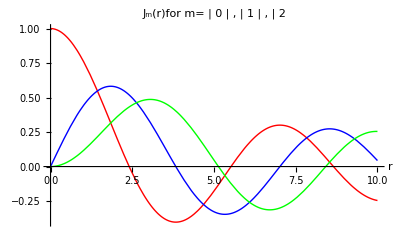

```mathematica
Plot[{BesselJ[0,r],BesselJ[1,r],BesselJ[2,r]},{r,0,10},PlotStyle->{Red,Blue,Green},PlotLabel->Grid[{{"J_m(r)for m=",Style["0",Red],",",Style["1",Blue],",",Style["2",Green]}},Spacings->0.3],AxesLabel->{"r"," "}]
```

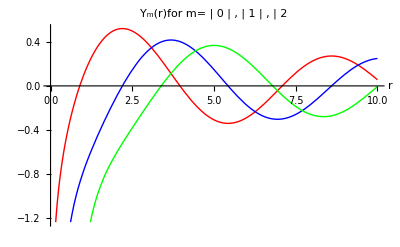

```mathematica
Plot[{BesselY[0,r],BesselY[1,r],BesselY[2,r]},{r,0,10},PlotStyle->{Red,Blue,Green},PlotLabel->Grid[{{"Y_m(r)for m=",Style["0",Red],",",Style["1",Blue],",",Style["2",Green]}},Spacings->0.3],AxesLabel->{"r"," "}]
```

The reader is invited to reevaluate these plots for different values of m and over different ranges of r in order to get a feel for the behavior of these functions.

One thing that is immediately apparent is that the Y_m's are all singular at the origin, due to the regular singular point there. Therefore, we can rule out these functions for the eigenmodes in our problem, and write

R(r̄)=A J_m( r̄).

#### Zeros of Bessel Functions

Another feature of Bessel functions also jumps out from the previous plots: like sines and cosines, these functions oscillate. In fact, one can think of J_m( r̄) and Y_m(r̄) as cylindrical coordinate versions of trigonometric functions.  Each function crosses through zero an infinite number of times in the range 0<r<∞. However, unlike trigonometric functions, the location of the zero crossings of the Bessel functions cannot be written down with any simple formula (except in certain limiting cases such as the zeros at large r: see the exercises for Sec. 5.2).

Starting with the smallest zero and counting upwards, we can formally refer to the nth zero of J_m( r̄)  as j_(m, n): that is,  J_m(j_(m,  n))=0, n = 1,2,3,... .Similarly, the nth zero of Y_m( r̄) is referred to as y_(m, n), and satisfies Y_m( y_(m, n))=0.

Although these zero crossings cannot be determined analytically, they can be found numerically. In fact, Mathematica has defined  the nth zero of Bessel function J_m  as BesseJZero[m,n]

```mathematica
BesseJZero[m,n]
```

BesseJZero[m,n]

The numerical value of the zeros is obtained by applying N. For instance, the first 10 consecutive zeros of  J_0(r) are

```mathematica
j0 =Table[BesselJZero[0,n],{n,1,10}]//N
```

{2.40483,5.52008,8.65373,11.7915,14.9309,18.0711,21.2116,24.3525,27.4935,30.6346}

Thus, the smallest zero of J_0(r), j_(0, 1), takes on the value j_(0, 1)=2.40483..., while the next is at  j_(0, 2)=5.52008..., and so on. Similarly, the first four consecutive zeros of J_1(r), {j_(1, 1),j_(1, 2),j_(1, 3),j_(1, 4)}, are obtained via

```mathematica
Table[BesselJZero[1,n],{n,1,4}]//N
```

{3.83171,7.01559,10.1735,13.3237}

Although we do not need them here, the nth zero of  the Y_m Bessel function can also be obtained  with the intrinsic function BesselYZero[m,n]. For instance,

```mathematica
Table[BesselYZero[2,n],{n,1,6}]//N
```

{3.38424,6.79381,10.0235,13.21,16.379,19.539}

#### Radial Eigenfunctions and Eigenvalues

The potential is zero on the tube sides at r=a. We can use our knowledge of the zeros of the Bessel function in order to match the resulting boundary condition  R(a)=0 . According to Eqs. (3.2.50) and (3.2.47), R(r)=A J_m(√κ r). Therefore, R(a) = A J_m(√κ a), so we must specify

κ = (j_(m, n)/a)^2,  n=1,2,3,...,

where j_(m, n)  is the nth zero of the mth Bessel function. This implies that the radial eigenfunctions R(r) are

R(r) = A J_m(j_(m, n)r/a).

A few of the m=0 radial eigenmodes are plotted in Cell 3.31. The list j0 of Bessel function zeros was defined in Cell 3.28.

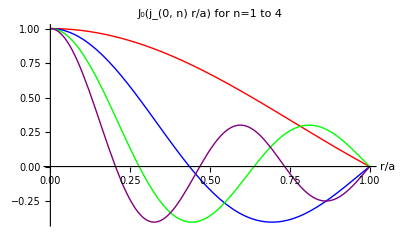

```mathematica
Plot[Evaluate[Table[BesselJ[0,j0[[n]] r],{n,1,4}]],{r,0,1},PlotStyle->{Red,Blue,Green,Purple},PlotLabel->"J_0(j_(0, n) r/a) for n=1 to 4",AxesLabel->{"r/a"," "}]
```

Eigenfunctions for other values of m can be plotted in the same way. This is left as an exercise for the reader.

#### The General Solution for ϕ

The full solution for ϕ  within the cylinder is obtained by summing over all radial eigenmodes, and all θ-eigenmodes:

ϕ(r,θ,z)=∑_(n=1)^∞ ∑_(m=-∞)^∞ A_(m n)J_m(j_(m, n) r/a) ⅇ^(ⅈ m θ)sinh (j_(m, n) z/a),

where the Fourier coefficients A_(m n) remain to be determined. This solution matches the homogenous boundary conditions on r=a and z=0. To satisfy the inhomogeneous boundary condition at z=L, namely  ϕ(r,θ,L)=ϕ_C(r,θ),  we choose the A_(m n)'s so that

ϕ_C(r,θ)=∑_(n=1)^∞ ∑_(m=-∞)^∞ A_(m n)J_m(j_(m, n) r/a) ⅇ^(ⅈ m θ)sinh (j_(m, n) L/a).

Putting aside the radial dependence for a moment, note that this is a Fourier series in θ. Application of the orthogonality relation for the Fourier modes ⅇ^(ⅈ m θ), Eq. (2.1.29), allows us to extract to extract a single value of m from the sum in the usual way:

∑_(n=1)^∞ A_(m n) sinh (j_(m, n) L/a)J_m(j_(m, n) r/a)= 1/(2π)∫_0^(2π) ⅆ θⅇ^(-ⅈ m θ)ϕ_C(r,θ).

However, this is not enough to determine A_(m n). It would be nice if there were some equivalent orthogonality relation that we could apply to the Bessel functions. Amazingly, such an orthogonality relation exists:

∫_0^a J_m(j_(m,n̄)r/a)J_m(j_(m,n)r/a)rⅆr=δ_(n n̄)a^2/2 J_(m+1)^2(j_(m,n)),

where δ_(n n̄) is a Kronecker delta function. Thus, for n≠ n̄, the different radial eigenmodes are orthogonal with respect to the radial integral ∫_0^a rⅆr.  This result can be checked using Mathematica:

```mathematica
Simplify[Integrate[BesselJ[m,Subscript[j, m ,n] r/a]BesselJ[m ,Subscript[j, m ,n̄] r/a] r,{r,0,a},Assumptions-> m≥ 0]/. BesselJ[m,Subscript[j, m ,n_]] ->  0]
```

0

```mathematica
FullSimplify[Integrate[BesselJ[m,Subscript[j, m ,n] r/a]^2  r,{r,0,a},Assumptions->m≥ 0&& Subscript[j, m,n]≥0], BesselJ[m,Subscript[j, m ,n]] == 0 ]
```

1/2 a^2 BesselJ[1+m,j_(m,n)]^2

We can use Eq. (3.2.55)  to extract a single term from the sum over n in Eq. (3.2.55). Multiplying both sides of the equation by J_m(j_(m,n̄)r/a) and applying the integral ∫_0^a rⅆr, we find

∑_(n=1)^∞ A_(m n) sinh (j_(m n) L/a)∫_0^a rⅆr J_m(j_(m,n̄)r/a) J_m(j_(m n) r/a)= 1/(2π)∫_0^a rⅆr J_m(j_(m,n̄)r/a)∫_0^(2π) ⅆ θⅇ^(-ⅈ m θ)ϕ_C(r,θ).

Substituting for the radial integral on the left-hand side using Eq. (3.2.55), we see that only the term with n=n̄ contributes, leaving us with the equation

A_(m n̄) sinh (j_(m n̄) L/a) a^2/2 J_(m+1)^2(j_(m,n̄))=1/(2π)∫_0^a rⅆr J_m(j_(m,n̄)r/a)∫_0^(2π) ⅆ θⅇ^(-ⅈ m θ)ϕ_C(r,θ).

This equation provides us with the Fourier coefficients A_(m n).

It is really quite surprising that the Bessel functions form an orthogonal set. It appears that every time we solve an eigenvalue problem, we obtain an orthogonal set of eigenmodes. The reasons for this will be discussed in Chapter 4.

A trivial extension of the same method used here could also be used to determine the form of the potential due to the nonzero potential at z=0,  ϕ(r,θ,0)=ϕ_B(r,θ). This part of the problem is left as an exercise.

#### Example

Say the potential on the top of the cylinder is fixed atϕ_C(r,θ)=V_o, and the other sides of the cylinder are grounded. Then according to Eq. (3.2.56), only the m=0 Fourier coefficients  A_(0 n) are nonzero, and the potential within the cylinder is given by Eq. (3.2.56) by a sum over the zeros of a single Bessel function, J_o:

ϕ(r,θ,z)=∑_(n=1)^∞ A_(0 n)J_0(j_(0 n) r/a) sinh (j_(0 n) z/a).

As expected from the symmetry of the problem, the potential is cylindrically symmetric. The Fourier coefficients are given by Eq. (3.2.56):

A_(0 n)=V_o/(a^2/2 J_1^2(j_(0,n))sinh (j_(0, n) L/a))∫_0^a rⅆr J_0(j_(0,n)r/a)

The required integral can be performed analytically using Mathematica :

```mathematica
A[n_] = V0/(a^2 BesselJ[1, j[n]]^2   Sinh[ j[n] L/a]/2) Integrate[r BesselJ[0,j[n] r/a],{r,0,a}]
```

(2 V0 Csch[(L j[n])/a])/(BesselJ[1,j[n]] j[n])

Here we have introduced the notation j[n]for the nth zero of the Bessel function J_o. This function can be defined in the following way:

```mathematica
j[n_] := BesselJZero[0,n]//N
```

Now the potential can be evaluated numerically, keeping the first 20 terms in the sum in Eq. (3.2.57):

```mathematica
ϕ[r_,z_] = Sum[A[n] BesselJ[0,j[n] r/a] Sinh[j[n] z/a],{n,1,20}];
```

This potential is plotted in Cell 3.37 as a contour plot, taking V_o=1 V, and L/a = 2.

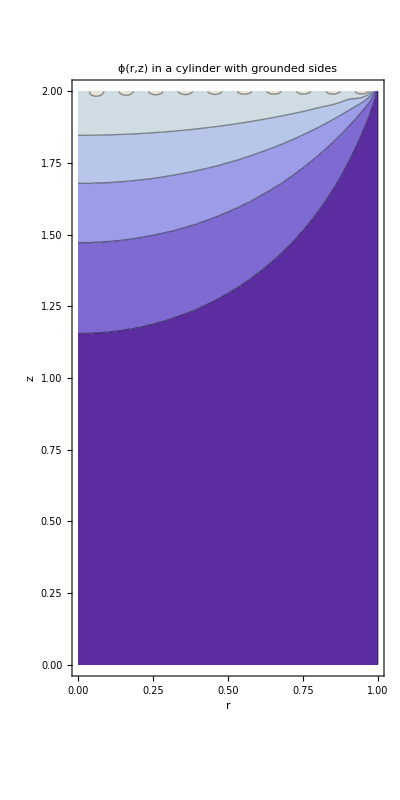

```mathematica
L=2 a; a=1; V0 = 1;
ContourPlot[ϕ[r,z],{r,0,a},{z,0,L},AspectRatio->2,FrameLabel->{"r","z"},PlotLabel->"ϕ(r,z) in a cylinder \n with grounded sides",ContourLabels->Automatic]
```

There is a Gibbs phenomenon near the top of the cylinder, because of the discontinuity in the potential between the top and the grounded sides.  However, this phenomenon dies away rapidly with distance from the top, leaving a well-behaved solution for the potential in the cylinder.

## Nonzero Potential on the Cylinder Sides: Modified Bessel Functions

We now consider the solution to the Laplace equation for a potential applied only to the sides of a cylinder of finite length L and radius a, ϕ(a,θ,z)=ϕ_A(θ,z).  On the ends of the cylinder at z=0 and z=L, the boundary conditions are ϕ=0.

This problem is still solved by a sum of terms of the form R(r) ⅇ^(ⅈ m θ) Z(z). Furthermore, separation of variables implies that  R(r)  and Z(z) are still governed by the same  ODEs, Eqs. (3.2.43) and (3.2.45), with the same general solutions, Eqs. (3.2.45) and (3.2.49).  However, the boundary conditions dictate that the coefficients in these general solutions must be chosen differently than in the previous case.

In order to satisfy ϕ(r,θ,0)=0, we require that B=-A in Eq. (3.2.45),  and in order to satisfy ϕ(r,θ,L)=0, we require that

κ^2=-(n π/L)^2,

so that Z(z) = 2 A ⅈ sin(n π z/L).   Now the z-equation has provided us with eigenmodes and eigenvalues, and they are standard trigonometric Fourier modes.

The radial solution R(r)  is still given by Eq. (3.2.49) but with the imaginary value of κ  given in Eq. (3.2.58):

R(r) = C J_m(ⅈ n π r/L ) + D Y_m(ⅈ n π r/L)

Bessel functions of an imaginary argument are called modified Bessel functions, I_m and K_m. These functions are defined below for integer m:

I_m(x) = ⅈ^-m J_m(ⅈ x) (for integer m);
K_m(x)=(π ⅈ^(m+1))/2[J_m(ⅈ x) + ⅈ Y_m(ⅈ x) ] (for integer m).

The modified Bessel functions bear a similar relation to J_m and Y_m to the one the hyperbolic functions sinh and cosh bear to the trigonometric functions sin and cos. In Mathematica, these functions are called BesselI[m,x] and
BesselK[m,x]. The first few modified Bessel functions are plotted in Cells 3.38 and 3.39.

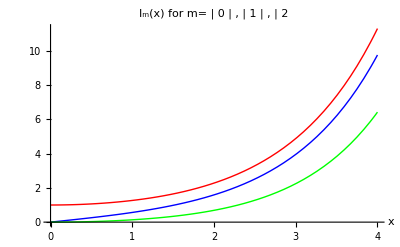

```mathematica
Plot[{BesselI[0,x],BesselI[1,x],BesselI[2,x]},{x,0,4},PlotStyle->{Red,Blue,Green},PlotLabel->Grid[{{"I_m(x) for m=",Style["0",Red],",",Style["1",Blue],",",Style["2",Green]}},Spacings->0.3],AxesLabel->{"x"," "}]
```

The I_m's are finite at the origin, but become exponentially large at large x.

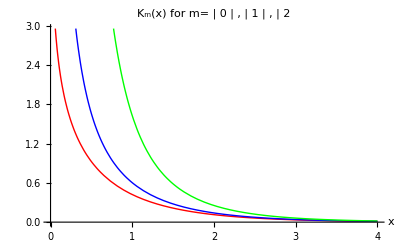

```mathematica
Plot[{BesselK[0,x],BesselK[1,x],BesselK[2,x]},{x,0,4},PlotStyle->{Red,Blue,Green},PlotLabel->Grid[{{"K_m(x) for m=",Style["0",Red],",",Style["1",Blue],",",Style["2",Green]}},Spacings->0.3],AxesLabel->{"x"," "}]
```

The K_m's are singular at the origin, but approach zero (with exponential rapidity) at large x.

The general solution for R(r) is, according to Eq. (3.2.59), a sum of I_m  and K_m. However, the previous plots show that only the I_m term should be kept, in order that the solution be finite at r=0. Therefore, we find that the radial function is R(r) = I_m(n π r/L), and the full solution for ϕ(r,θ,z) is a linear combination of these functions:

ϕ(r,θ,z)=∑_(m=-∞)^∞ ∑_(n=1)^∞ B_(n m)I_m(n π r/L)ⅇ^(ⅈ m θ)sin(n π z/L).

The Fourier coefficients a_(m n) are determined by matching to the inhomogeneous boundary condition at r=a:

ϕ(a,θ,z)=ϕ_A(θ,z)=∑_(m=-∞)^∞ ∑_(n=1)^∞ B_(n m)I_m(n π a/L)ⅇ^(ⅈ m θ)sin(n π z/L).

Since this sum is a regular Fourier series in both θ and z, we can use orthogonality of the trigonometric functions  to find the Fourier coefficients:

B_(n m) I_m(n π a/L)=1/(π L)∫_0^(2π) ⅆθ ⅇ^(-ⅈ m θ)∫_0^L ⅆz sin(n π z/L) ϕ_A(θ,z) .

This completes the problem of determining the potential inside a cylindrical tube of finite length. More examples of such problems are left to the exercises.

Exercises for Sec. 3.2

(1) Solve  ∇^2 ϕ(x,y)=0 for the following boundary conditions Plot the solutions using Plot3D.

(a) ϕ(0,y)=ϕ(2,y)=ϕ(x,0)=0; ϕ(x,1)=1.

(b) (∂ϕ)/(∂x)(0,y)=(∂ϕ)/(∂x)(1,y)=(∂ϕ)/(∂y)(x,0)=0;  (∂ϕ)/(∂y)(x,1)=cos 2 π n x, n  an integer. (What happens for n=0?)

(c) ϕ(0,y)=2; ϕ(1,y)=ϕ(x,0)=0; (∂ϕ)/(∂y)(x,1)=1.

(d) (∂ϕ)/(∂x)(0,y)=(∂ϕ)/(∂x)(1,y)=(∂ϕ)/(∂y)(x,0)=0, (∂ϕ)/(∂y)(x,1)=1.

(2) A battery consists of a cube of side L filled with fluid of conductivity σ. The electrodes in the battery consist of two plates on the base at y=0, one grounded and one at potential V=12 Volts (see Fig. 3.13). The other sides of the battery casing are not conductive. Find the potential ϕ everywhere inside the battery.

Fig. 3.13 Exercise (2).

(3) Find the solution to ∇^2 ϕ(r,θ)=0 inside a 2D cylinder for the following boundary conditions. Plot the solutions using  contour plots.

(a) ϕ(1,θ)=cos n θ, n an integer.

(b) ϕ(1,θ)= 0 for x>0; ϕ(1,θ)=1 for x<0.

(c)  ϕ(1,θ)=0, ϕ(2,θ)=h(θ) (find ϕ between the concentric cylinders, h is a Heaviside step function, -π<θ<π assumed)

(d) (∂ϕ)/(∂r)(1,θ)=sin 2 θ, ϕ(2,θ)=cos θ (find ϕ between the concentric cylinders).

(4) A long conducting cylinder of radius a=5 cm has a sector of opening angle α=20° that is electrically isolated from the rest of the cylinder by small gaps (see Fig. 3.14). The sector is placed at potential V_o=1 Volt. Find the potential and plot it  throughout the cylinder.

Fig. 3.14 Exercise (4).

(5)(a)  The bottom and top of the of the wedge shown in Fig. 3.15 are grounded, but the end at r=a is held at V=5 V. Find the potential everywhere inside the wedge by using separation of variables, and plot is as a surface plot for α=30°.

Fig. 3.15 Exercise (5).

(b) Show that the radial electric field near r=0 is singular near r=0 if α >π, and find the form of the singularity [Answer: E_r ∝r^(π/α -1)sin (π θ/α) as r→ 0.]

(6) An electrolytic cell consists of two plastic concentric cylinders of radii a and b, a<b, and length L. Between the cylinders is an acid with conductivity σ. Two conducting vanes of width b-a and length L are placed in the cell between the cylinders, parallel to the axis of the cell, one along the positive x-axis and one along the negative x-axis. If the vanes are held at a fixed potential difference V_o, find the total current running between the vanes. Plot the contours of constant potential. [Hint: The potential satisfies Laplace's equation with Neumann boundary conditions at the nonconducting surfaces and Dirichlet conditions at the conductors: see Exercise (2) above and Example 2 in Sec. 3.2.2. Be careful to keep all  of the radial eigenmodes, including the n=0 (constant) mode.]

(7) Find the solution to ∇^2 Ψ(r,θ,ϕ)=0 inside a sphere with the following boundary conditions.

(a) Ψ(1,θ,ϕ)=sin^2 θ.

(b) Ψ(1,θ,ϕ)=V_o θ^2(π-θ).

(c) (∂Ψ)/(∂r)(1,θ,ϕ)=sin2θ cosϕ.

(8) A conducting sphere of radius a=2 cm is cut in half (see Fig. 3.16). The left half is grounded,  and the right half is at 10V.  Find the electrostatic potential ϕ(r,θ) everywhere outside the sphere, assuming that the potential goes to zero at infinity. Plot the potential for a<r<6 cm.

Fig. 3.16 Exercise (8).

(9) Two concentric spheres have radii a and b (b>a). Each is divided into two hemispheres by the same horizontal plane. The upper hemisphere of the outer sphere and the lower hemisphere of the inner sphere are maintained at potential V. The other hemispheres are grounded. Determine the potential in the region a≤ r≤ b in terms of Legendre polynomials. Plot the result for b=3a/2.

(10) A grounded conducting sphere of radius a is placed with its center at the origin, in a uniform electric field E = E ẑ that is created by an external potential ϕ_e=-E z.  Find the total potential ϕ(r) outside the sphere. (Hint: ϕ=0 at r=a; write ϕ_e in spherical coordinates.)

(11) By applying the Taylor expansion function Series to the Bessel functions, investigate the small-x form of J_m(x) and Y_m(x). Answer the following questions:

(a) Find a simple analytic expression for J_m(x) (m an integer)  as x approaches zero. Does your expression apply for m<0 as well as m>0?

(b) The Y_m's are singular near the origin. Find the form of the singularity for m=0,1,2,....

(12) Repeat the previous Exercise for the modified Bessel functions I_m(x) and K_m(x) (m an integer).

(13) A cylinder has length L=1 meter and radius a=1/2 meter. The sides and the top of the cylinder are grounded, but the base at z=0 is held at potential V=50 V. Find the potential ϕ(r,z) throughout the interior. Plot the result using ContourPlot.

(14) A cylinder of unit height and radius has grounded ends, at z=-1/2 and z=1/2. The cylindrical wall  at r=1 is split in half lengthwise along the x=0 plane. The half with x>0 is held at 10 V, and the half for which x<0 is grounded. Find the potential and obtain the value of the electric field, -∇ϕ (magnitude and direction),  at the origin. Plot the potential in the z=0  plane using a surface plot.

(15) In a Penning-Malmberg  trap,  used to trap charged particles with static electric and magnetic fields,  potentials are applied to coaxial cylindrical electrodes of radius a, shown in Fig. 3.17,  in order to provide an axial trapping potential.

Fig. 3.17 Exercise (15).

(a) Find the potential ϕ(r,z) in the central region around r=0 as a Fourier series involving the Bessel function I_0.

(b) Taylor-expand this expression in  r and z to show that the potential near r=0 has the form

ϕ(r,z) = A r^2 + B z^2+C .

This form of ϕ is simply an even Taylor expansion in r and z, as required by the symmetry of the system. Find values for A, B, and C  when a=5 cm, b=5 cm, and L=10 cm.

(c) By direct substitution of Eq. (3.2.62)  into Laplace's equation, show that A=-B/2. This implies that the center of the trap is a saddlepoint of the potential.  Does your solution from part (a) satisfy this?

(d) By carefully taking a limit as L→ ∞, show that your result from part (a) can be written as the following Fourier integral:

ϕ(r,z)=V_o(1-2/π∫_0^∞ ⅆk/k sin k b cos k z (I_o(k r))/(I_o(k a))).

[Hint: Mathematica can do the following sum analytically: ∑_(n=0)^∞ (-1)^n/(2n+1). ] Use the integral form to plot ϕ(0,z)  for -2b≤ z≤ 2b, taking a=b/2.

(16) A cylindrical copper bar of conductivity σ has radius a and length L, with 0<z<L. The surface of the bar is insulated, except on the ends at r=0, where wires are attached. The wire at z=r=0 injects current I, and the wire at r=0, z=L removes the same current. Therefore, the form of the current density at z=0 and L is j(r,z=0)=j(r,z=L)=I (δ(r))/(2 π r) ẑ.  Find the electrostatic potential ϕ(r,z) throughout the bar, and plot it as a contour plot, in suitably normalized coordinates, assuming that ϕ(0,L/2)=0. Show that your solution satisfies 2π∫_0^a rⅆr j_z(r,z)=I, and plot j_z(r,L/2) vs. r. (Hint: keep all eigenmodes, including one with a zero eigenvalue. See Example 2 in Sec. 3.2.2.)

## 3.3 The Wave and Heat Equations in Two and Three Dimensions

In a uniform medium, the wave and heat equations in one dimension have the form ∂^2 z/∂t^2=c^2∂^2 z/∂x^2 and ∂T/∂t=χ∂^2 T/∂x^2 respectively. In multiple spatial dimensions,  the obvious generalization of these equations is

∂^2 z/∂t^2=c^2∇^2 z(r,t)

and

∂T/∂t=χ∇^2 T(r,t),

where ∇^2  is the Laplacian operator, Eq. (3.2.2). This generalization allows the evolution of disturbances without any distinction between different spatial directions: the equations are isotropic in space.

We now consider solutions of the heat and wave equations within some specified region V, which has a surface S (see Fig. 3.8). Boundary conditions of either Dirichlet, Neumann, or mixed form are specified on this surface, just as in the solution of Laplace's equation. Initial conditions must also be provided throughout the region. As in the one-dimensional case, two initial conditions (on z and ∂z/∂t) are required for the wave equation, but only one initial condition specifying  T(r,t=0) is required for the heat equation.

General solutions for these equations can be found. The form of the solutions is a superposition of normal modes, just as for the one-dimensional cases discussed in Sec. 3.1.  However, for most boundary conditions, the normal modes cannot be determined analytically.  Analytically tractable solutions can be obtained only for those special geometries in which the modes are separable. (Numerical solutions can be found using methods to be discussed in Chapter 6.)  In this section we consider several examples where the normal modes can be found using separation of variables.

3.3.1 Heat Equation with Rectangular Boundaries

Separation of variables can be used to determine the evolution of temperature T(x,y,t) in the rectangular region defined by 0<x<a, 0<y<b. The temperature is  assumed to be known in this region at the initial time t=0,

T(x,y,t=0) = T_0(x,y).

Furthermore, the temperature on the rectangular boundaries is fixed at T=T_s(x,y) (i.e. a Dirichlet boundary condition is assumed). The solution to the heat equation (3.3.2) that satisfies these boundary conditions can then be written as

T(x,y,t) = T_eq(x,y) + ΔT(x,y,t)

where T_eq is the equilibrium solution for the temperature, and ΔT is the deviation from equilibrium. The equilibrium solution satisfies the time-independent  version of the heat equation.

∇^2 T_eq(x,y) = 0,

with the boundary conditions that T_eq=T_s on the rectangular boundaries. This is just Laplace's equation, which can be solved using the methods discussed in Sec 3.2.2. The deviation from equilibrium satisfies the heat equation,

∂/(∂t)ΔT=χ (ϑ^2/ϑx^2+ϑ^2/ϑy^2)ΔT(x,y,t),

with homogeneous boundary conditions that ΔT=0 on the boundaries, since T_eqalready satisfies the boundary conditions. Using separation of variables,  a possible solution of this equation can be constructed as a product of functions of x, y, and t :

ΔT=f(t)X(x)Y(y).

Substituting this into Eq. (3.3.6) and dividing by ΔT yields

1/(f(t))(∂f)/(∂t)=χ (1/(X(x))(ϑ^2 X)/ϑx^2+1/(Y(y))(ϑ^2 Y)/ϑx^2),

which separates into three ODEs:

ϑ^2/ϑx^2 X=-k_x^2X(x),

ϑ^2/ϑy^2 Y=-k_y^2Y(y),

ϑ/ϑt f=-χ(k_x^2+k_y^2)f(t),

where -k_x^2 and -k_y^2 are separation constants. These constants are determined by the boundary condition that ΔT=0 on the boundaries, which implies X(0)= X(a)=Y(0)=Y(a)=0. With these homogeneous boundary conditions, Eqs. (3.3.8) and (3.3.9) are familiar eigenvalue problems, with eigenvalues and eigenfunctions given by

k_x=n π/a,  k_y=m π/b,

X(x)=sin(n π x/a),  Y(y)=sin (m π y/b),

for nonnegative integers n and m. The exponential time dependence f(t) of each mode then  follows immediately from the solution of Eq. (3.3.10). A superposition of all possible modes provides the general homogeneous Dirichlet solution to Eq. (3.3.6) in the rectangular region,

ΔT(x,y,t) = ∑_(n,m=1)^∞ A_(m,n)ⅇ^(-χπ^2(n^2/a^2+m^2/b^2)t)sin(n π x/a)sin(m π y/b).

The constants A_(m,n) follow from the initial condition, Eq. (3.3.3). Substituting for ΔT from Eq. (3.3.13) yields

∑_(n,m=1)^∞ A_(m,n)sin(n π x/a)sin(m π y/b)=T_o(x,y)-T_eq(x,y).

The left and side is a double Fourier sine series  in x and y, so the Fourier coefficients follow immediately as

A_(m,n)=4/(a b)∫_0^a ⅆx∫_0^b ⅆy sin(n π x/a)sin(m π y/b)[T_o(x,y)-T_eq(x,y)].

This completes the solution to the problem. An example evolution is shown in Cell 3.39  for the case a=2,b=1, T_o=1, χ=1, and zero temperaure on the boundaries, so that T_eq=0.

```mathematica
Clear["Global`*"]
Subscript[T, o]=1; a=2;b=1;χ=1;
A[m_,n_] = 4/(a b)Integrate[Subscript[T, o] Sin[n π x/a]Sin[m π y/b],{x,0,a},{y,0,b}];
T[x_,y_,t_] = Sum[A[m,n] Exp[-χ π^2(n^2/a^2+m^2/b^2)t]Sin[n π x/a]Sin[m π y/b],{n,1,15},{m,1,15}];
ListAnimate[Table[Plot3D[T[x,y,t],{x,0,a},{y,0,b},BoxRatios->{a/b,1,.5},PlotRange->{0,1.1}],{t,1/160,1/4,1/40}]]
```

As time progresses , the initially uniform temperature quickly diffuses out through the zero-temperature boundaries.

3.3.2 Oscillations of a Circular Drumhead

## General solution

Consider a drum consisting of a 2D membrane stretched tightly over a circular ring in the x-y plane, of radius a. The membrane is free to vibrate in the transverse (z) direction, with an amplitude z(r,θ,t), where r and θ are polar coordinates in the x-y plane. These vibrations satisfy the wave equation (3.3.1). The wave propagation speed is c=√(T/σ), where T is the tension force per unit length applied to the edge of the membrane, and σ is the mass per unit area of the membrane. Since the membrane is fixed to the ring at r=a, the boundary condition on z is

z(a,θ,t)=0.

The initial conditions are

z(r,θ,0)=z_o(r,θ),
(∂z)/(∂t)(r,θ,0)=v_o(r,θ)

for some initial transverse displacement and velocity, z_o and v_o respectively.

To solve for the evolution of z, we use separation of variables, assuming a solution of the form:

z(r,θ,t) =f(t) R(r) e^(ⅈ m θ),

for integer m. Substituion of this form into Eq. (3.3.1) and division by z leads in the usual way to  separate ODEs for the time and space dependence:

ⅆ^2/(ⅆ t^2)f(t) =-ω^2f(t),

where ω is a separation constant (the normal mode frequency), and

1/r∂/(∂r)(r(∂ R)/(∂r))-m^2/r^2 R= -ω^2/c^2R.

Equation (3.3.20) can be recognized as Bessel's equation, Eq. (3.2.48), with general solution

R(r) =A J_m(ω r/c)+B Y_m(ω r/c) .

The frequency is determined by the condition that the solution is bounded at r=0, which implies B=0, and the boundary condition (3.3.16) which implies

ω =c j_(m,n)/a≡ω_(m,n).

Therefore the radial dependence of the mode is

R(r) = J_m(j_(m, n)r/a),

and the time dependence is given by the solution of Eq. (3.3.19),

f(t) = A cos ω_(m,n) t + B sin ω_(m,n) t.

A linear superposition of all possible values of m and n yields the general soution to the wave equation on a circular drumhead,

z(r,θ,t) =∑_(m=-∞)^∞ ∑_(n=1)^∞ (A_(m,n)cos ω_(m,n)t+B_(m,n)sin ω_(m,n)t)J_m(j_(m,n)r/a)ⅇ^(ⅈ m θ).

The constants A_(m,n) and B_(m,n) are  determined by the initial conditions, just as for the one-dimensional wave equation. To determine A_(m,n), we evaluate Eq. (3.3.25) at time t=0, and using Eq. (3.3.17)  we find

z(r,θ,0) = ∑_(m,n) A_(m,n) J_m(j_(m,n)r/a)ⅇ^(ⅈ m θ)=z_o(r,θ).

The constants A_(m,n) can be extracted just as we did for Laplaces equation, using Eq. (3.2.55):

A_(m,n)=1/(2π)∫_0^a rⅆr J_m(j_(m,n̄)r/a)∫_0^(2π) ⅆ θⅇ^(-ⅈ m θ)z_o(r,θ)/(a^2/2 J_(m+1)^2(j_(m,n))).

Similarly, one finds that

ω_(m,n)B_(m,n)=1/(2π)∫_0^a rⅆr J_m(j_(m,n̄)r/a)∫_0^(2π) ⅆ θⅇ^(-ⅈ m θ)v_o(r,θ)/(a^2/2 J_(m+1)^2(j_(m,n))).

This completes the solution of the problem. One can see that, aside from the higher-dimensionality of the  normal modes, the solution procedure is formally identical to that for the 1-dimensional string.

Although the eigenmodes are complex, the coefficients A_(m n) and B_(m n) are also complex, so that the series sums to a real quantity z(r,θ,t).  In particular, Eqs. (3.3.27)  and (3.3.28) imply that the coefficients satisfy A_(-m n)=A_(m n)^* and B_(-m n)=B_(m n)^*. Also, Eq. (3.3.22) implies that ω_(-m n)= ω_(m n). If we use these results in Eq. (3.3.25) we can write the solution as a sum only over nonnegative m  as

z(r,θ,t)=∑_(n=1)^∞ (A_(0 n)cos ω_(0 n)t + B_(0 n)sin ω_(0 n)t)J_0(j_(0, n)r/a)+ ∑_(m=1)^∞ ∑_(n=1)^∞ ( [A_(m n)ⅇ^(ⅈ m θ)+A_(m n)^*ⅇ^(-ⅈ m θ)]cos ω_(m n)t 
        + [B_(m n)ⅇ^(ⅈ m θ)+B_(m n)^*ⅇ^(-ⅈ m θ)]sin ω_(m n)t ) J_m(j_(m, n)r/a).

The quantities in the square brackets are real; for example, A_(m n)ⅇ^(ⅈ m θ)+A_(m n)^*ⅇ^(-ⅈ m θ)= 2 Re(A_(m n)ⅇ^(ⅈ m θ)). In fact, if we write A_(m n)=|A_(m n)| ⅇ^(ⅈ ϕ_(m n)^A), and B_(m n)= |B_(m n)|ⅇ^(ⅈ ϕ_(m n)^B) where ϕ_(m n)^A and  ϕ_(m n)^Bare the complex phases of the amplitudes, then Eq. (3.3.29) becomes

z(r,θ,t)=∑_(n=1)^∞ (A_(0 n)cos ω_(0 n)t + B_(0 n)sin ω_(0 n)t)J_0(j_(0, n)r/a)+
 2∑_(n=1)^∞ ∑_(m=1)^∞ [|A_(m n)|cos(θ + ϕ_(m n)^A)cos ω_(m n)t +|B_(m n)|cos(θ + ϕ_(m n)^B)sinω_(m n)t]  J_m(j_(m, n)r/a) .

This result is manifestly real, and shows directly that the complex part of the Fourier amplitudes merely produces a phase shift in the θ-dependence of the Fourier modes.

## Drumhead Eigenmodes

The cylindrically symmetric modes of the drumhead correspond to m=0, and have frequencies ω_(0 n)= j_(0, n) c/a. Unlike the modes of a uniform string, these frequencies are not commensurate:

ω_01=2.40483c/a,ω_02=5.52008c/a,ω_03=8.65373c/a,...

These m=0 modes have no θ-dependence. Like string modes, they are standing waves with stationary nodes at specific radial locations. In the lowest-order mode, the entire drumhead oscillates up and down, while in higher order modes different sections of the drumhead are oscillating 180° out of phase with the center. One of these modes, the m=0, n=3 mode, is shown in Cell 3.40.

```mathematica
j0=BesselJZero[0,3]//N;

ψ[r_,θ_] = BesselJ[0,j0 r] ;

Table[ParametricPlot3D[{r Cos[θ],r Sin[θ],Cos[t]ψ[r,θ]},{r,0,1},{θ,0,2 Pi},PlotRange->{-1,1},BoxRatios->{1,1,1/2}],{t,0,1.8 Pi, .2 Pi}];

ListAnimate[%,AnimationRate->5]
```

For m≠ 0, the eigenmodes obviously  have  θ-dependence ⅇ^(ⅈ m θ)=cos m θ + ⅈ sin m θ. As discussed above in relation to Eq. (3.3.30)  the real and imaginary parts simply correspond to oscillations that are shifted in θ by 90°.  Just as for the cylindrically symmetric (m=0) modes, there are radial nodes where the drumhead is stationary. However, there are also locations in θ where nodes occur. This can be seen in Cell 3.41, which plots the real part of the m=1, n=2 mode. For this mode, the line θ=π/2 (the y-axis) is stationary.

```mathematica
j1 = BesselJZero[1,2]//N;
ψ[r_,θ_] = BesselJ[1,j1 r] Cos[θ];

Table[ParametricPlot3D[{r Cos[θ],r Sin[θ],Cos[t]ψ[r,θ]},{r,0,1},{θ,0,2 Pi},PlotRange->{-1,1},BoxRatios->{1,1,1/2},AxesLabel->{"x","y","z"}],{t,0,1.8 Pi, .2 Pi}];

ListAnimate[%,AnimationRate->5]
```

The reader is invited to plot some of the other modes in this manner, so as to get a feeling for their behavior.

## Traveling Waves in θ

We have found that the general solution to the 2D wave equation is a sum of eigenmodes with oscillatory time-dependence, given by Eq. (3.3.25). Each term in the sum has the form

(A_(m n)cos ω_(m n)t + B_(m n)sin  ω_(m n)t) ⅇ^(ⅈ m θ)J_m(j_(m, n)r/a).

Let 's consider a specific case, where the complex amplitude B_(m n) equals -ⅈ A_(m n) for some given m and n. For this mode, expression (3.3.31)  can be written as

A_(m n) (cos ω_(m n)t - ⅈ sin ω_(m n)t) ⅇ^(ⅈ m θ)J_m(j_(m, n)r/a)=A_(m n) ⅇ^(-ⅈ ω_(m n)t)ⅇ^(ⅈ m θ)J_m(j_(m, n)r/a)
=A_(m n) ⅇ^(ⅈ( m  θ-ω_(m n)t))J_m(j_(m ,n)r/a)

This mode is a traveling wave in the θ-direction. The real part of the mode has a θ-variation of the form cos(m θ-ω_(m n)t + ϕ_(m n)^A), so this wave moves, unlike a standing wave. For example, at t=0, there is a maximum in the real part of the wave at m θ+ϕ_(m n)^A=0; but as time progresses this maximum moves according to the equation m θ-ω_(m n)t+ϕ_(m n)^A=0, or θ=-ϕ_(m n)^A/m+(ω_(m n)/m)t.

The angular velocity ω_(m n)/m is also called the phase velocity c_ϕ of this wave. Since the wave is moving in θ, this phase velocity has units of radians per second. In Chapter 5, we will consider traveling waves moving linearly in r. There, the phase velocity has units of meters per second.

We could also choose B_(m n)=+ⅈ A_(m n) in Eq. (3.3.31). This results in a traveling wave proportional to  ⅇ^(ⅈ( m  θ+ω_(m n)t)). This wave travels in the -θ direction.

In Cell 3.42 we exhibit an animation of the drumhead traveling wave for  m=1,n=1 , traveling in the positive θ-direction.

```mathematica
m=1; ω=j1=BesselJZero[1,1]//N;

ψ[r_,θ_,t_] = BesselJ[1,j1  r] Cos[m θ-ω t];

Table[ParametricPlot3D[{r Cos[θ],r Sin[θ],ψ[r,θ,t]},{r,0,1},{θ,0,2 Pi},BoxRatios->{1,1,1/2}],{t,0,1.9 Pi/ω, .1 Pi/ω}];

ListAnimate[%,AnimationRate->8]
```

## Static Inhomogeneous Boundary Conditions

Static inhomogeneous boundary conditions can be handled in a manner analogous to that used for the one-dimensional wave equation , as discussed in Sec. 3.1.2 , and the multiidimensional heat equation discussed in Sec. 3.3.1. Sources or time-dependent boundary conditions are covered using the methods discussed in Chapter 4.

For example, on a circular drumhead the rim might be warped, with a height that is given by some function z_o(θ). This implies a Dirichlet boundary condition

z(a,θ)=z_o(θ).

The wave equation is then solved by breaking the solution into a two pieces, z(r,θ,t)=Δz(r,θ,t) +z_eq(r,θ), wherez_eq is the equilibrium solution and Δz is the deviation from equilibrium. The equilibrium solution satisfies the time-independent wave-equation,

c^2∇^2 z_eq=0

which is just Laplace's equation, solved with the boundary condition  (3.3.32).  The deviation from equilibrium has homogeneous boundary conditions and is given by Eq. (3.3.25). Thus, warping the drumhead rim does not affect the normal modes. (Of course, this assumes that the warping is small, since we are using the linear wave equation to describe its effect.)

The equilibrium solution be found using the Laplace solution methods discussed in Sec. 3.2.3.  For instance, if the warped edge follows the equation z(a,θ)= a sin2θ, the solution to Laplace's equation that matches this boundary condition is simply z_eq(r,θ)=( r^2/a) sin2θ. [This follows from Eq. (3.1.24), and can be verified by direct substitution into ∇^2 z_eq=0.] This equilibrium shape is displayed in Cell 3.43.

```mathematica
Subscript[z, eq][r_,θ_] = r^2 Sin[2 θ];

ParametricPlot3D[{r Cos[θ],r Sin[θ],Subscript[z, eq][r,θ]},{r,0,1},{θ,0,2 Pi},BoxRatios->{1,1,1/2},PlotLabel->"equilibrium of a warped circular drumhead"]
```

-Graphics3D-

3.3.3 Large-Scale Ocean Modes

The large-scale waves of the ocean provide an instructive example of waves in spherical geometry. Here, for simplicity we take the idealized case of a "water world", where the ocean completely covers the earth's surface, with uniform depth d_o<< R, where  R is the radius of the earth. Also, we will neglect the effects of earth's rotation on the wave dynamics.

As we saw in Exercise (4) of Sec. 3.1, waves in shallow water (for which the wavelength >> d_o) satisfy a wave equation with speed c=√(g d_o), where g=9.8 m/s^2  is the acceleration of gravity. On the spherical surface of the earth, these waves will also satisfy the wave equation, written in  spherical coordinates. That is, the depth of the ocean now varies according to d=d_o+h(θ,ϕ,t), where h is the change in height of the surface due to the waves, at latitude and longitude specified by the spherical polar angles θ and ϕ.  The function h satisfies the wave equation,

∂^2 h/∂t^2=c^2∇^2 h(θ,ϕ,t)=c^2/R^2(1/sinθ∂/(∂θ)(sinθ(∂h)/(∂θ))+1/(sin^2 θ)(∂^2 h)/(∂ϕ^2)),

where we have used the spherical form of ∇^2 , Eq. (3.2.27) [see Lamb (1932, pg. 301)].

Separation of variables can be applied to this equation. Using the usual approach, a solution for h can be found of the form

h(θ,ϕ,t)=f(t)Y_(l, m)(θ,ϕ),

where Y_(l,m) is a spherical harmonic, defined in Eq. (3.2.39). Substitutiing Eq. (3.3.35) into Eq. (3.3.34), and using Eqs. (3.2.30) , and (3.2.34), implies that  f satisfies  harmonic oscillator equation (3.3.19) with mode frequency ω  given by

ω = c√(l(l+1))/R≡ω_l.

The full solution of Eq. (3.3.34) is a sum of these normal modes,

h(θ,ϕ,t)=∑_(l=0)^∞ ∑_(m=-l)^l (A_(l m)cos ω_l t + B_(l m)sin ω_l t)Y_(l, m)(θ,ϕ).

It is entertaining to work out the frequencies and shapes of some of the low-order modes, for earth-like parameters. Taking an average ocean depth of roughly  d_o= 4 km, the wave speed is c=√(9.8×4000)m/s=198 m/s. The earth's radius is approximately R=6400 km, so the lowest-frequency modes, with l=1, have frequency ω_1=√2 c/R=4.4×10^-5 s^-1 , corresponding to a period of 2π/ω_1=1.4×10^5 s, or 40 hours. The l=2 modes have a frequency that is larger by the factor √3, giving a period of 23 hours.  The l=1 and 2 modes are shown in Cells 3.45 and 3.45, for m=0.

```mathematica
l=1; m=0;
Table[ParametricPlot3D[(1 +.4Cos[t]SphericalHarmonicY[l,m,θ,ϕ]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,Pi},{ϕ,0,2Pi},PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}}],{t,0,2Pi-0.2Pi,.2 Pi}];
ListAnimate[%,AnimationRate-> 5]
```

In the l=1,m=0 mode, water moves from pole to pole, with the result that the center of mass of the water oscillates axially. Such motions could actually only occur if there were a time-dependent force acting to accelerate the water with respect to the solid portion of the earth, such as an undersea earthquake, or a meteor impact (see the exercises). Of course, such events also excite other modes.

The next azimuthally-symmetric mode has l=2,  and is showin in Cell 3.45.

```mathematica
l=2; m=0;
Table[ParametricPlot3D[(1 +.2Cos[t]SphericalHarmonicY[l,m,θ,ϕ]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,Pi},{ϕ,0,2Pi},PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}}],{t,0,2Pi-0.2Pi,.2 Pi}];
ListAnimate[%,AnimationRate->5]
```

In this l=2,m=0 mode, water flows from the equator to the poles and back, producing elliptical perturbations. The reader is invited to explore the behavior of other modes  by reevaluating these animations for different l-values.

Oscillations with m≠ 0 are also of great importance. Of particular interest is the traveling-wave form of the l=m=2 perturbation, which is an elliptical distortion of the ocean surface that travels around the equator. This mode is actually a linear combination of the l=2, m=±2 spherical harmonics, and can most easily be expressed in terms of the associated Legendre functions  making up these harmonics: Y_(2, ±2)∝ P_2^2(cosθ) ⅇ^(ⅈ(±2 ϕ - ω_2 t)). [Here we have used the fact that P_2^-2(cosθ)is proportional to P_2^2(cosθ); see Table 3.2 in Sec. 3.2.4.] The resulting disturbance is shown in Cell 3.46.

```mathematica
l=2; m=2;
Table[ParametricPlot3D[(1 +.05LegendreP[l,m,Cos[θ]]Cos[m ϕ -  t]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,Pi},{ϕ,0,2Pi},PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}}],{t,0,2Pi-0.2Pi,.2 Pi}];
ListAnimate[%,AnimationRate->5]
```

This type of elliptical traveling wave can be excited by the gravitational attraction of the earth to the moon. The moon appears to revolve about the earth daily in the earth's rest frame. This revolution, in concert with the earth-moon attraction, causes an elliptical distortion that follows the moon's apparent position, and is responsible for the earth's tides [see Eq. (4.3.80)]. It is interesting that the natural frequency of this mode is 23 hours for the parameters that we chose; this means that the mode is almost resonant with the gravitational force caused by the moon (in our simple model, that is - on the real earth, there are many effects neglected here, not least of which are the continents, which tend to get in the way of this mode).

Exercises for Sec. 3.3

(1)(a) Find the frequencies and spatial form of the normal modes of oscillation of a rectangular trampoline with length a, width b, and propagation speed c.

(b) Determine the evolution of a square trampoline with fixed edges of length L=3 m and wave speed c=3 m/s.  Neglect gravity. The initial conditions are ż=0,  z(x,y,0)=t(x)t(y), where t(x) is a triangular shape,

t(x)={x,           x<L/2,
L-x,  x>L/2..

Animate this evolution for 0<t< 2 s using Plot3D.

(2) One edge of the frame of a square drumhead with unit sides is warped, following z(0,y)=(1/4 )sin(2 π y). The other edges are straight, satisfying z=0. Find z(x,y) in equilibrium, and plot it as a surface plot using Plot3D.

(3) A french fry has a square cross section with sides of length a=1 cm and an overall length of L=5 cm. The fry is initially at a uniform temperature T=0 °C . It is tossed into boiling fat at T=150 °C. How long does it take for the center of the fry to reach 100°C ? Take χ = 2×10^-7 m^2/s.

(4) A cooling vane on a motor has the shape of a thin square with sides of length a=0.7 cm with thickness d = 0.2 cm (see Fig. 3.18). Initially, the motor is off and the vane is at uniform temperature T=300K. When the motor is turned on, a constant heat flux Γ= 500 W/cm^2  enters one thin edge of the vane, and the five other faces are all  kept at T=300 K. The thermal conductivity of the vane is  κ=0.1 W/(cm K),and the specific heat is C=2 J/(cm^3 K).

(a) Find the equilibrium temperature distribution, and determine what is the maximum temperature in the vane, and where it occurs.

(b)  Plot the temperature vs. time as a sequence of contour plots in x and y at z=d/2 for 0<t<0.5 s.

Fig. 3.18 Exercise (4).

(5) Solve for the motion of a circular drumhead with a fixed boundary of radius a=1and sound speed c=1, subject to the following initial conditions:

(a) z(r,θ,0)=(r^2(1-r))^3 cos4θ,∂_t z(r,θ,0)=0. Animate the solution for 0<t<2 using Plot3D.

(b) z(r,θ,0)=0,∂_t z(r,θ,0)=δ(r)/r. Animate the solution for 0<t<2 using Plot.

(6) Solve the following heat equation problems in cylindrical coordinates:

(a) T(r,θ,0)=δ(r)/r in an insulated cylinder of radius a=1 and thermal diffusivity χ=1. Animate the solution for 0<t<0.5.

(b) T(r,θ,0)=0, in a cylinder of radius a=1, thermal diffusivity χ=1 and thermal conductivity κ=1. There is an incident heat flux Γ=-cosθ r̂.

(7) Damped waves on a circular drumhead, radius a, satisfy the following PDE:

γ (∂z(r,θ,t))/(∂t)+(∂^2 z(r,θ,t))/(∂t^2)=c^2∇^2 z(r,θ,t), where γ>0 is a damping rate.

(a) Find the eigenmodes and eigenfrequencies for this wave equation, assuming that the edge of the drumhead at r=a  is fixed.

(b) Solve for the motion given the initial conditions z(r,θ,0)=(1-r )r^2 sin2θ , ż(r,θ,0)=0, and boundary condition z(1,θ,t)=0. Animate the solution for γ=0.3, c=1, 0<t<2.

(8) A can of beer, radius a=3 cm and height L=11 cm, is initially at room temperature T=25 °C. The beer is placed in a cooler of ice, at 0°C.  Solve the heat equation to determine how long it takes the beer to cool to less than 5°C. Assume that the thermal diffusivity is that of water, χ=1.4×10^-7m^2/s.

(9) A drumhead has the shape of a wedge, shown in Fig. 3.19, with opening angle α. The edges of the drumhead are fixed at z=0. Find analytic expressions for the frequencies and spatial forms of the normal modes for this drumhead. Find the lowest frequency mode, for α=27°, and plot its form as a surface plot. Plot the frequency of this mode as a function of α for 0<α<360°.

Fig. 3.19 Exercise (6).

(10) A wheel of radius R=10 cm rotates on a bearing of radius a=1 cm, with angular frequency ω=100 rad/sec. The surface of the wheel is insulated, except at the bearing. At time t=0 the wheel has uniform temperature T_o=300 K, but due to friction on the bearing it begins to heat. Taking the torque due to friction as τ=1 newton per meter of length of the bearing, the heating power per unit length is τ ω=100 W/m. Assuming that this power is dissipated into the metal wheel, with the thermal conductivity and heat capacity of copper, find T(r,t) in the wheel.

(11) A meteor strikes the north pole of a spherical planet of radius a=5000 km, covered with water of uniform depth d_o=1 km. The acceleration of gravity on the planet is g=10 m/s^2. Initially, the perturbed ocean height satisfies h(θ,ϕ,0)=h_o exp(-50 θ^2), ∂_t h(θ,ϕ,0)=0, where h_o=100 m. Find the evolution h(θ,ϕ,t) of the subsequent tidal wave, and animate it versus time using Plot (as a function of θ only) for 0<t<50 hours.

(12) A child drops a pebble into the center of a shallow pool of water of radius a=1 m and depth h. The wave height z(r,t) satisfies the wave equation, with  wave propagation speed  c=√(g h)=1 m/s.  The initial disturbance has the form z(r,0)= -z_oexp(-30  r^2)(1-30 r^2), ∂_t z(r,0)=0, where z_o=1 cm (and r is measured in meters). The boundary condition at the pool edge is not Dirichlet: the water surface at the pool edge can move up and down. To find the correct boundary condition, we must consider the radial displacement η of fluid during the wave motion.

(a) Using the same techniques as were used in the derivation of Eq. (3.1.78), show that the radial fluid displacement η is related to the wave height z by

z = -h/r ∂(r η)/∂r.

(b) The boundary conditions are η=0 at r=a, and η  finite at r=0. Find the eigenmodes and eigenfrequencies, and plot the wave height z vs. r  for the first three eigenmodes.

(c) Solve the initial-value problem stated previously, and animate the solution using Plot for 0<t<2.

(13) For bounded pools of shallow water with waves moving in one dimension only, we saw in the previous problem that it is necessary to consider the horizontal fluid displacement η(r,t). For general wave motion, this displacement is  a vector, η(r,t).Wave height z is related to fluid displacement according to z=-h∇·η.  Using the same method as that which led to Eq. (3.1.78), one can show that η satisfies the vector equation

∂^2/(∂t^2)η(r,t)=c^2∇∇·η(r,t)

where c=√(g h), for a pool with constant equilibrium depth h. The boundary condition on this equation is n̂·η=0, where n̂ is a unit vector normal to the edge of the pool.

(a) Using Eq. (3.3.38) show that wave height z satisfies a wave equation.

(b) Assume that η=∇ϕ(r,t). This is called potential flow [see Landau and Lifshitz (1959)]. Show that ϕ also satisfies the wave equation

∂^2/(∂t^2) ϕ=c^2∇^2 ϕ

with Neumann boundary condition  n̂·∇ϕ=0. Show that ϕ and z are related according to z=-h ∇^2 ϕ.

(14)(a) A coffee cup has radius a and is filled with coffee of depth h.  Assuming potential flow and using Eq. (3.3.39) with r=(r,θ), find analytic expressions for the frequency and spatial form of the normal modes of the coffee. What is spatial form and frequency of the lowest frequency mode? (Hint: This mode is not cylindrically symmetric.) Plot the spatial form of z(r,θ,t) for this mode. 
(b) Find the frequency of this lowest mode for a cup of radius a=3 cm, filled to a depth of h=1 cm. See if you can set this mode up in your coffee. Measure its frequency with your watch, and use a ruler to determine the depth of the coffee and the cup diameter. Compare to the theory, and discuss any errors.

## References

Arthur C. Clarke, The Fountains of Paradise (Harcourt Brace Jovanovitch, New York, 1979).

L. D. Landau and E.M. Lifshitz, Fluid Mechanics (Pergamon, London, 1959).

D. G. Zill and M. R. Cullen, Advanced Engineering Mathematics, 2nd ed.  (Jones and Bartlett, Sudbury, Mass., 2000).